```mathematica
Quit[];
```

# Two fluid solutions to anisotropic static spherically symmetric spacetimes for a quadratic model of gravity.

## Article ref: arXiv:2403.00070

Author: Mariam Campbell

Affiliation: University of Cape Town
Email: CMPMAR009@myuct.ac.za

Any enquiries about this file post 2025 can be sent to mariam.campbell09@gmail.com.
This notebook only contains the solutions calculated in the the notebook “Completer stellar reconstruction case I.nb”.
NOTE: the expressions for the matter fluid are the conserved quantities

## Solutions presented considers Y_(Interior Schwarzschild) and 𝒦_(Tolman IV)

### Ricci scalar

```mathematica
R[r_,μ1_,c_,A_,ℛ_]:=((2 (A^4 (3 c^2 (3-r^2 μ1)^(3/2)+√(3-r^2 μ1) (6 r^4 μ1^2+9 (3+ℛ^2 μ1)-2 r^2 μ1 (15+ℛ^2 μ1))+c (9 r^4 μ1^2+9 (6+ℛ^2 μ1)-2 r^2 μ1 (24+ℛ^2 μ1)))+2 r^2 (c^2 (3 r^2+ℛ^2) (3-r^2 μ1)^(3/2)+3 c (6 ℛ^2-16 r^4 μ1+3 r^6 μ1^2+r^2 (18-ℛ^2 μ1))+√(3-r^2 μ1) (9 ℛ^2+6 r^6 μ1^2+3 r^2 (9+ℛ^2 μ1)-r^4 μ1 (30+ℛ^2 μ1)))+A^2 (c^2 (7 r^2+3 ℛ^2) (3-r^2 μ1)^(3/2)+c (54 ℛ^2+22 r^6 μ1^2+r^4 μ1 (-117+ℛ^2 μ1)-6 r^2 (-21+2 ℛ^2 μ1))+√(3-r^2 μ1) (27 ℛ^2+15 r^6 μ1^2-r^4 μ1 (75+2 ℛ^2 μ1)+r^2 (63+6 ℛ^2 μ1)))))/((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2))
```

```mathematica
R[r,Subscript[μ, 1],Subscript[c, 1],A,ℛ]
```

(2 (A^4 (3 c_1^2 (3-r^2 μ_1)^(3/2)+√(3-r^2 μ_1) (6 r^4 μ_1^2+9 (3+ℛ^2 μ_1)-2 r^2 μ_1 (15+ℛ^2 μ_1))+c_1 (9 r^4 μ_1^2+9 (6+ℛ^2 μ_1)-2 r^2 μ_1 (24+ℛ^2 μ_1)))+2 r^2 ((3 r^2+ℛ^2) c_1^2 (3-r^2 μ_1)^(3/2)+3 c_1 (6 ℛ^2-16 r^4 μ_1+3 r^6 μ_1^2+r^2 (18-ℛ^2 μ_1))+√(3-r^2 μ_1) (9 ℛ^2+6 r^6 μ_1^2+3 r^2 (9+ℛ^2 μ_1)-r^4 μ_1 (30+ℛ^2 μ_1)))+A^2 ((7 r^2+3 ℛ^2) c_1^2 (3-r^2 μ_1)^(3/2)+c_1 (54 ℛ^2+22 r^6 μ_1^2+r^4 μ_1 (-117+ℛ^2 μ_1)-6 r^2 (-21+2 ℛ^2 μ_1))+√(3-r^2 μ_1) (27 ℛ^2+15 r^6 μ_1^2-r^4 μ_1 (75+2 ℛ^2 μ_1)+r^2 (63+6 ℛ^2 μ_1)))))/((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ_1) (3-r^2 μ_1+c_1 √(3-r^2 μ_1))^2)

### Total pressure: p^T

```mathematica
pT[r_,μ1_,c_,A_,ℛ_]:=(-A^2 (c^2 (7 r^2+3 ℛ^2) (3-r^2 μ1)^(3/2)+√(3-r^2 μ1) (27 ℛ^2+r^2 (63+30 ℛ^2 μ1+r^2 μ1 (-108+23 r^2 μ1-7 ℛ^2 μ1)))+2 c (27 ℛ^2+r^2 (63+6 ℛ^2 μ1+r^2 μ1 (-75+15 r^2 μ1-2 ℛ^2 μ1))))-2 r^2 (c^2 (3 r^2+ℛ^2) (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3 ℛ^2+r^2 (9+4 ℛ^2 μ1+r^2 μ1 (-14+3 r^2 μ1-ℛ^2 μ1)))+2 c (9 ℛ^2+r^2 (27+3 ℛ^2 μ1+r^2 μ1 (-30+6 r^2 μ1-ℛ^2 μ1))))-A^4 (3 c^2 (3-r^2 μ1)^(3/2)+√(3-r^2 μ1) (27+18 ℛ^2 μ1+r^2 μ1 (-42+9 r^2 μ1-4 ℛ^2 μ1))+2 c (27+μ1 (9 ℛ^2+6 r^4 μ1-2 r^2 (15+ℛ^2 μ1)))))/(3 (A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2)
```

```mathematica
pT[r,Subscript[μ, 1],Subscript[c, 1],A,ℛ]//.(√(3-r^2 Subscript[μ, 1]))->𝓏
```

(-A^2 ((7 r^2+3 ℛ^2) c_1^2 (3-r^2 μ_1)^(3/2)+𝓏 (27 ℛ^2+r^2 (63+30 ℛ^2 μ_1+r^2 μ_1 (-108+23 r^2 μ_1-7 ℛ^2 μ_1)))+2 c_1 (27 ℛ^2+r^2 (63+6 ℛ^2 μ_1+r^2 μ_1 (-75+15 r^2 μ_1-2 ℛ^2 μ_1))))-2 r^2 ((3 r^2+ℛ^2) c_1^2 (3-r^2 μ_1)^(3/2)+3 𝓏 (3 ℛ^2+r^2 (9+4 ℛ^2 μ_1+r^2 μ_1 (-14+3 r^2 μ_1-ℛ^2 μ_1)))+2 c_1 (9 ℛ^2+r^2 (27+3 ℛ^2 μ_1+r^2 μ_1 (-30+6 r^2 μ_1-ℛ^2 μ_1))))-A^4 (3 c_1^2 (3-r^2 μ_1)^(3/2)+𝓏 (27+18 ℛ^2 μ_1+r^2 μ_1 (-42+9 r^2 μ_1-4 ℛ^2 μ_1))+2 c_1 (27+μ_1 (9 ℛ^2+6 r^4 μ_1-2 r^2 (15+ℛ^2 μ_1)))))/(3 (A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ_1) (3+𝓏 c_1-r^2 μ_1)^2)

### Total energy density: μ^T

```mathematica
μT[r_,μ1_,c_,A_,ℛ_]:=(3 A^4+2 r^2 (3 r^2+ℛ^2)+A^2 (7 r^2+3 ℛ^2))/((A^2+2 r^2)^2 ℛ^2)
```

### Total radial pressure: p_r^T

```mathematica
prT[r_,μ1_,c_,A_,ℛ_]:=(4 (A^2+r^2) (-r^2+ℛ^2) (1/4-((A^2+2 r^2) ℛ^2)/(4 (A^2+r^2) (-r^2+ℛ^2))+(r^2 μ1)/(-6+2 r^2 μ1-2 c √(3-r^2 μ1))))/(r^2 (A^2+2 r^2) ℛ^2)
```

```mathematica
prT[r,Subscript[μ, 1],Subscript[c, 1],A,ℛ]
```

(4 (A^2+r^2) (-r^2+ℛ^2) (1/4-((A^2+2 r^2) ℛ^2)/(4 (A^2+r^2) (-r^2+ℛ^2))+(r^2 μ_1)/(-6+2 r^2 μ_1-2 c_1 √(3-r^2 μ_1))))/(r^2 (A^2+2 r^2) ℛ^2)

### Total orthogonal pressure: (p_⊥)^T:

```mathematica
pperpT[r_,μ1_,c_,A_,ℛ_]:=(-2 r^4 (c^2 (3-r^2 μ1)^(3/2)+√(3-r^2 μ1) (9+6 ℛ^2 μ1+r^2 μ1 (-15+3 r^2 μ1-ℛ^2 μ1))+c (18+6 ℛ^2 μ1+r^2 μ1 (-21+4 r^2 μ1-ℛ^2 μ1)))+A^4 (-c^2 (3-r^2 μ1)^(3/2)+c (-18-6 ℛ^2 μ1+r^2 μ1 (21-4 r^2 μ1+ℛ^2 μ1))+√(3-r^2 μ1) (-9-6 ℛ^2 μ1+r^2 μ1 (15-3 r^2 μ1+ℛ^2 μ1)))-A^2 (c^2 (2 r^2+ℛ^2) (3-r^2 μ1)^(3/2)+3 c (6 ℛ^2+r^2 (12+μ1 (-16 r^2+ℛ^2+3 r^4 μ1)))+√(3-r^2 μ1) (9 ℛ^2+r^2 (18+9 ℛ^2 μ1+r^2 μ1 (-36+7 r^2 μ1-ℛ^2 μ1)))))/((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2)
```

```mathematica
pperpT[r,Subscript[μ, 1],Subscript[c, 1],A,ℛ]//.√(3-r^2 Subscript[μ, 1])->𝓏
```

(-2 r^4 (c_1^2 (3-r^2 μ_1)^(3/2)+𝓏 (9+6 ℛ^2 μ_1+r^2 μ_1 (-15+3 r^2 μ_1-ℛ^2 μ_1))+c_1 (18+6 ℛ^2 μ_1+r^2 μ_1 (-21+4 r^2 μ_1-ℛ^2 μ_1)))+A^4 (-c_1^2 (3-r^2 μ_1)^(3/2)+c_1 (-18-6 ℛ^2 μ_1+r^2 μ_1 (21-4 r^2 μ_1+ℛ^2 μ_1))+𝓏 (-9-6 ℛ^2 μ_1+r^2 μ_1 (15-3 r^2 μ_1+ℛ^2 μ_1)))-A^2 ((2 r^2+ℛ^2) c_1^2 (3-r^2 μ_1)^(3/2)+3 c_1 (6 ℛ^2+r^2 (12+μ_1 (-16 r^2+ℛ^2+3 r^4 μ_1)))+𝓏 (9 ℛ^2+r^2 (18+9 ℛ^2 μ_1+r^2 μ_1 (-36+7 r^2 μ_1-ℛ^2 μ_1)))))/((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ_1) (3+𝓏 c_1-r^2 μ_1)^2)

### Energy density for the matter fluid: μ_m

```mathematica
μm[r_,α_,μ1_,c_,A_,ℛ_]:=-((A^10 (-3 c^4 (ℛ^2+6 α) (3-r^2 μ1)^(7/2)+4 c^3 (135 ℛ^4 α μ1^2-3 α (486-936 r^2 μ1+444 r^4 μ1^2-104 r^6 μ1^3+9 r^8 μ1^4)+ℛ^2 (-3 r^8 μ1^4+36 r^2 μ1 (9+α μ1)+4 r^6 μ1^3 (9+α μ1)-6 r^4 μ1^2 (27+7 α μ1)-81 (3+8 α μ1)))+(3-r^2 μ1)^(3/2) (-2 ℛ^4 α μ1^2 (-513+12 r^2 μ1+4 r^4 μ1^2)+18 α (-81+300 r^2 μ1-54 r^4 μ1^2+4 r^6 μ1^3)-3 ℛ^2 (81+864 α μ1+r^8 μ1^4+2 r^4 μ1^2 (27-58 α μ1)+4 r^6 μ1^3 (-3+2 α μ1)+36 r^2 μ1 (-3+16 α μ1)))-2 c^2 √(3-r^2 μ1) (ℛ^4 α μ1^2 (-1053+48 r^2 μ1-4 r^4 μ1^2)+3 α (1458-3672 r^2 μ1+1452 r^4 μ1^2-304 r^6 μ1^3+23 r^8 μ1^4)+ℛ^2 (9 r^8 μ1^4+18 r^4 μ1^2 (27-5 α μ1)+4 r^6 μ1^3 (-27+4 α μ1)+243 (3+16 α μ1)+36 r^2 μ1 (-27+20 α μ1)))+12 c (-3+r^2 μ1) (2 ℛ^4 α μ1^2 (-108+5 r^2 μ1)+2 α (243-756 r^2 μ1+222 r^4 μ1^2-36 r^6 μ1^3+2 r^8 μ1^4)+ℛ^2 (r^8 μ1^4+2 r^4 μ1^2 (27-29 α μ1)+6 r^6 μ1^3 (-2+α μ1)+81 (1+8 α μ1)+12 r^2 μ1 (-9+23 α μ1))))+16 r^6 (-c^4 (-3 ℛ^4 α+3 r^4 (ℛ^2+3 α)+r^2 (ℛ^4+6 ℛ^2 α)) (3-r^2 μ1)^(7/2)-2 c^3 (-486 ℛ^4 α+3 r^12 (2 ℛ^2+9 α) μ1^4+2 r^10 μ1^3 (-156 α+ℛ^4 μ1+4 ℛ^2 (-9+α μ1))+162 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))-6 r^8 μ1^2 (-222 α+ℛ^4 μ1 (4+α μ1)+ℛ^2 (-54+17 α μ1))+36 r^6 μ1 (-78 α+ℛ^4 μ1 (3+2 α μ1)+ℛ^2 (-18+17 α μ1))-27 r^4 (-54 α+6 ℛ^2 (-3+4 α μ1)+ℛ^4 μ1 (8+17 α μ1)))-c^2 √(3-r^2 μ1) (-1458 ℛ^4 α+3 r^12 (6 ℛ^2+23 α) μ1^4+486 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))+2 r^10 μ1^3 (-456 α+3 ℛ^4 μ1+2 ℛ^2 (-54+13 α μ1))-81 r^4 (-18 ℛ^2-54 α+ℛ^4 μ1 (8+25 α μ1))-2 r^8 μ1^2 (-2178 α+ℛ^4 μ1 (36+11 α μ1)+9 ℛ^2 (-54+29 α μ1))+12 r^6 μ1 (-918 α+ℛ^4 μ1 (27+22 α μ1)+6 ℛ^2 (-27+37 α μ1)))-(3-r^2 μ1)^(3/2) (-243 ℛ^4 α+3 r^12 ℛ^2 μ1^4+r^10 μ1^3 (-36 α+ℛ^4 μ1+18 ℛ^2 (-2+α μ1))+81 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))+6 r^6 μ1 (-450 α+ℛ^4 μ1 (9+8 α μ1)+18 ℛ^2 (-3+11 α μ1))-27 r^4 (-27 α-3 ℛ^2 (3+8 α μ1)+ℛ^4 μ1 (4+25 α μ1))+r^8 μ1^2 (486 α+ℛ^4 μ1 (-12+α μ1)-6 ℛ^2 (-27+41 α μ1)))+4 c (-3+r^2 μ1) (-243 ℛ^4 α+3 r^12 (ℛ^2+2 α) μ1^4+81 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))+r^10 μ1^3 (-108 α+ℛ^4 μ1+3 ℛ^2 (-12+5 α μ1))-27 r^4 (-27 α-3 ℛ^2 (3+4 α μ1)+2 ℛ^4 μ1 (2+9 α μ1))+3 r^6 μ1 (-756 α+ℛ^4 μ1 (18+17 α μ1)+6 ℛ^2 (-18+41 α μ1))-3 r^8 μ1^2 (-222 α+ℛ^4 μ1 (4+α μ1)+ℛ^2 (-54+53 α μ1))))+4 A^4 r^2 (-c^4 (-25 ℛ^4 α+6 r^2 ℛ^2 (2 ℛ^2+α)+3 r^4 (12 ℛ^2+49 α)) (3-r^2 μ1)^(7/2)-2 c^3 (-4050 ℛ^4 α+2 r^12 (36 ℛ^2+199 α) μ1^4+r^8 μ1^2 (19449 α-ℛ^4 μ1 (288+5 α μ1)+54 ℛ^2 (72+11 α μ1))+6 r^6 μ1 (-7200 α+81 ℛ^2 (-16+3 α μ1)+ℛ^4 μ1 (216+11 α μ1))+108 r^2 (9 ℛ^2 α+2 ℛ^4 (9+23 α μ1))+2 r^10 μ1^3 (-2307 α+12 ℛ^4 μ1-ℛ^2 (432+29 α μ1))-18 r^4 (-1323 α-12 ℛ^2 (27+32 α μ1)+2 ℛ^4 μ1 (72+109 α μ1)))-(3-r^2 μ1)^(3/2) (-2025 ℛ^4 α+9 r^12 (4 ℛ^2-α) μ1^4+6 r^10 μ1^3 (-13 α+2 ℛ^4 μ1+6 ℛ^2 (-12+α μ1))+54 r^2 (9 ℛ^2 α+2 ℛ^4 (9+17 α μ1))-18 r^6 μ1 (2154 α+ℛ^2 (216-903 α μ1)+ℛ^4 μ1 (-36+65 α μ1))+r^8 μ1^2 (3537 α-18 ℛ^2 (-108+95 α μ1)+2 ℛ^4 μ1 (-72+101 α μ1))-27 r^4 (-441 α+2 ℛ^4 μ1 (24+131 α μ1)-4 ℛ^2 (27+146 α μ1)))+4 c (-3+r^2 μ1) (-2025 ℛ^4 α+4 r^12 (9 ℛ^2+17 α) μ1^4+54 r^2 (9 ℛ^2 α+2 ℛ^4 (9+19 α μ1))-9 r^4 (-1323 α-324 ℛ^2 (1+4 α μ1)+8 ℛ^4 μ1 (18+67 α μ1))+r^10 μ1^3 (-1248 α+12 ℛ^4 μ1+ℛ^2 (-432+73 α μ1))+r^8 μ1^2 (7524 α+ℛ^2 (1944-897 α μ1)+ℛ^4 μ1 (-144+77 α μ1))-3 r^6 μ1 (11016 α-18 ℛ^2 (-72+161 α μ1)+ℛ^4 μ1 (-216+181 α μ1)))-c^2 √(3-r^2 μ1) (-12150 ℛ^4 α+6 r^12 (36 ℛ^2+155 α) μ1^4+972 r^2 (3 ℛ^2 α+2 ℛ^4 (3+7 α μ1))+2 r^10 μ1^3 (-6189 α+36 ℛ^4 μ1+ℛ^2 (-1296+67 α μ1))-18 r^4 (-3969 α+16 ℛ^4 μ1 (27+65 α μ1)-36 ℛ^2 (27+70 α μ1))+r^8 μ1^2 (57519 α+ℛ^2 (11664-618 α μ1)+ℛ^4 μ1 (-864+121 α μ1))-18 r^6 μ1 (9108 α+ℛ^4 μ1 (-216+65 α μ1)-3 ℛ^2 (-432+391 α μ1))))+2 A^6 (-c^4 (129 ℛ^4 α+3 r^4 (14 ℛ^2+47 α)+10 r^2 (ℛ^4-11 ℛ^2 α)) (3-r^2 μ1)^(7/2)+4 c (-3+r^2 μ1) (10449 ℛ^4 α+21 r^12 (2 ℛ^2-α) μ1^4+r^10 μ1^3 (-339 α+10 ℛ^4 μ1+ℛ^2 (-504+29 α μ1))+r^8 μ1^2 (4680 α+ℛ^2 (2268-561 α μ1)+8 ℛ^4 μ1 (-15+34 α μ1))-162 r^2 (55 ℛ^2 α+ℛ^4 (-5+84 α μ1))-6 r^6 μ1 (5859 α+ℛ^2 (756-1383 α μ1)+5 ℛ^4 μ1 (-18+85 α μ1))+9 r^4 (1269 α+42 ℛ^2 (9+64 α μ1)+2 ℛ^4 μ1 (-60+89 α μ1)))-2 c^3 (20898 ℛ^4 α+2 r^12 (42 ℛ^2+187 α) μ1^4+4 r^10 μ1^3 (-1083 α+5 ℛ^4 μ1-6 ℛ^2 (42+11 α μ1))+3 r^8 μ1^2 (6099 α+5 ℛ^4 μ1 (-16+21 α μ1)+6 ℛ^2 (252+167 α μ1))-108 r^2 (165 ℛ^2 α+ℛ^4 (-15+256 α μ1))+18 r^4 (1269 α+4 ℛ^4 μ1 (-30+163 α μ1)+6 ℛ^2 (63+296 α μ1))-12 r^6 μ1 (3645 α+42 ℛ^2 (18+17 α μ1)+ℛ^4 μ1 (-90+307 α μ1)))+(3-r^2 μ1)^(3/2) (-10449 ℛ^4 α+3 r^12 (-14 ℛ^2+45 α) μ1^4-2 r^10 μ1^3 (696 α+5 ℛ^4 μ1-9 ℛ^2 (28+α μ1))+270 r^2 (33 ℛ^2 α+ℛ^4 (-3+50 α μ1))+36 r^6 μ1 (1161 α-6 ℛ^2 (-21+89 α μ1)+ℛ^4 μ1 (-15+94 α μ1))+r^8 μ1^2 (1323 α-8 ℛ^4 μ1 (-15+56 α μ1)+18 ℛ^2 (-126+101 α μ1))+27 r^4 (-423 α+2 ℛ^4 μ1 (20+29 α μ1)-2 ℛ^2 (63+524 α μ1)))-c^2 √(3-r^2 μ1) (62694 ℛ^4 α+14 r^12 (18 ℛ^2+47 α) μ1^4-36 r^6 μ1 (4752 α+ℛ^2 (756-77 α μ1)+9 ℛ^4 μ1 (-10+39 α μ1))+4 r^10 μ1^3 (-2430 α+15 ℛ^4 μ1-ℛ^2 (756+71 α μ1))+18 r^4 (3807 α+40 ℛ^4 μ1 (-9+34 α μ1)+54 ℛ^2 (21+124 α μ1))-324 r^2 (165 ℛ^2 α+ℛ^4 (-15+254 α μ1))+r^8 μ1^2 (49023 α+54 ℛ^2 (252+79 α μ1)+ℛ^4 μ1 (-720+1141 α μ1))))+8 A^2 r^4 (-c^4 (-45 ℛ^4 α+r^4 (16 ℛ^2+51 α)+6 r^2 (ℛ^4+9 ℛ^2 α)) (3-r^2 μ1)^(7/2)-(3-r^2 μ1)^(3/2) (-3645 ℛ^4 α+2 r^12 (8 ℛ^2-3 α) μ1^4+6 r^10 μ1^3 (-13 α+ℛ^4 μ1+16 ℛ^2 (-2+α μ1))+r^8 μ1^2 (1890 α+ℛ^4 μ1 (-72+11 α μ1)-54 ℛ^2 (-16+27 α μ1))-27 r^4 (-153 α-8 ℛ^2 (6+7 α μ1)+3 ℛ^4 μ1 (8+63 α μ1))+54 r^2 (81 ℛ^2 α+ℛ^4 (9+86 α μ1))+6 r^6 μ1 (-2574 α+ℛ^4 μ1 (54+43 α μ1)+9 ℛ^2 (-32+161 α μ1)))+4 c (-3+r^2 μ1) (-3645 ℛ^4 α+r^12 (16 ℛ^2+27 α) μ1^4+r^8 μ1^2 (3240 α+ℛ^2 (864-1047 α μ1)-2 ℛ^4 μ1 (36+13 α μ1))+162 r^2 (27 ℛ^2 α+ℛ^4 (3+29 α μ1))+r^10 μ1^3 (-525 α+6 ℛ^4 μ1+ℛ^2 (-192+95 α μ1))-9 r^4 (-459 α+36 ℛ^2 (-4+α μ1)+2 ℛ^4 μ1 (36+227 α μ1))+6 r^6 μ1 (-2160 α+ℛ^4 μ1 (54+67 α μ1)+3 ℛ^2 (-96+323 α μ1)))-2 c^3 (-7290 ℛ^4 α+r^12 (32 ℛ^2+151 α) μ1^4+2 r^10 μ1^3 (-873 α+6 ℛ^4 μ1+ℛ^2 (-192+41 α μ1))+108 r^2 (81 ℛ^2 α+ℛ^4 (9+89 α μ1))-2 r^8 μ1^2 (-3672 α+ℛ^4 μ1 (72+41 α μ1)+ℛ^2 (-864+501 α μ1))-9 r^4 (-918 α+24 ℛ^2 (-12+37 α μ1)+ℛ^4 μ1 (144+611 α μ1))+6 r^6 μ1 (-2664 α+ℛ^4 μ1 (108+161 α μ1)+ℛ^2 (-576+975 α μ1)))-c^2 √(3-r^2 μ1) (-21870 ℛ^4 α+r^12 (96 ℛ^2+365 α) μ1^4+324 r^2 (81 ℛ^2 α+ℛ^4 (9+88 α μ1))+2 r^10 μ1^3 (-2451 α+18 ℛ^4 μ1+ℛ^2 (-576+197 α μ1))-18 r^8 μ1^2 (-1278 α+ℛ^4 μ1 (24+13 α μ1)+ℛ^2 (-288+227 α μ1))+6 r^6 μ1 (-10476 α+ℛ^4 μ1 (324+457 α μ1)+3 ℛ^2 (-576+1297 α μ1))-9 r^4 (-2754 α+288 ℛ^2 (-3+5 α μ1)+ℛ^4 μ1 (432+2201 α μ1))))+A^8 (-c^4 (5 r^2 (5 ℛ^2-8 α)+3 (ℛ^4+52 ℛ^2 α)) (3-r^2 μ1)^(7/2)+4 c (-3+r^2 μ1) (r^10 (25 ℛ^2-198 α) μ1^4+6 r^6 μ1^2 (-798 α+ℛ^2 (225-724 α μ1)+3 ℛ^4 μ1 (-2+α μ1))+243 (52 ℛ^2 α+ℛ^4 (1+8 α μ1))+r^8 μ1^3 (1782 α+3 ℛ^4 μ1+20 ℛ^2 (-15+19 α μ1))+18 r^4 μ1 (-480 α+ℛ^4 μ1 (9+7 α μ1)+50 ℛ^2 (-3+23 α μ1))-9 r^2 (360 α+9 ℛ^2 (-25+132 α μ1)+4 ℛ^4 μ1 (9+157 α μ1)))-4 c^3 (r^10 (25 ℛ^2-22 α) μ1^4+6 r^4 ℛ^2 μ1 (-450+1731 α μ1+ℛ^2 μ1 (27+7 α μ1))+81 (156 ℛ^2 α+ℛ^4 (3+8 α μ1))-2 r^6 μ1^2 (666 α+2 ℛ^4 μ1 (9+α μ1)+75 ℛ^2 (-9+14 α μ1))+r^8 μ1^3 (270 α+3 ℛ^4 μ1+2 ℛ^2 (-150+89 α μ1))-9 r^2 (360 α+2 ℛ^4 μ1 (18+77 α μ1)+3 ℛ^2 (-75+548 α μ1)))+(3-r^2 μ1)^(3/2) (-25 r^10 (ℛ^2-12 α) μ1^4+54 r^4 μ1 (240 α+ℛ^2 (50-538 α μ1)+ℛ^4 μ1 (-3+2 α μ1))-81 (156 ℛ^2 α+ℛ^4 (3+32 α μ1))-3 r^8 μ1^3 (1044 α+ℛ^4 μ1+4 ℛ^2 (-25+34 α μ1))+27 r^2 (120 α+5 ℛ^2 (-15+64 α μ1)+4 ℛ^4 μ1 (3+79 α μ1))+2 r^6 μ1^2 (4536 α+2 ℛ^4 μ1 (9-26 α μ1)+3 ℛ^2 (-225+952 α μ1)))-6 c^2 √(3-r^2 μ1) (5 r^10 (5 ℛ^2-18 α) μ1^4+81 (156 ℛ^2 α+ℛ^4 (3+16 α μ1))+r^8 μ1^3 (766 α+3 ℛ^4 μ1+ℛ^2 (-300+278 α μ1))-3 r^2 (1080 α+9 ℛ^2 (-75+472 α μ1)+2 ℛ^4 μ1 (54+545 α μ1))-2 r^6 μ1^2 (1104 α+2 ℛ^4 μ1 (9+2 α μ1)+ℛ^2 (-675+1516 α μ1))+2 r^4 μ1 (-2160 α+ℛ^4 μ1 (81+65 α μ1)+3 ℛ^2 (-450+2413 α μ1)))))/((A^2+2 r^2)^5 ℛ^4 (3-r^2 μ1)^(3/2) (3-r^2 μ1+c √(3-r^2 μ1))^4))
```

### Radial pressure for the matter fluid: p_r^m

```mathematica
prm[r_,α_,μ1_,c_,A_,ℛ_]:=-((4 ℛ^4 ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))) (-8 r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) α (-3+r^2 μ1) (-6+3 r^2 μ1-2 c √(3-r^2 μ1)) (-3+r^2 μ1-c √(3-r^2 μ1))-8 (A^2+2 r^2)^2 ℛ^2 α (-3+r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^2+2 r^2)^2 ℛ^2 (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^2+8 (A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) α √(3-r^2 μ1) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-4 r^2 ℛ^2 √(3-r^2 μ1) (A^4 (2 c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6-6 r^2 μ1+ℛ^2 μ1+r^4 μ1^2)+c (36-30 r^2 μ1+3 ℛ^2 μ1+5 r^4 μ1^2))+2 r^4 (2 c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6-6 r^2 μ1+ℛ^2 μ1+r^4 μ1^2)+c (36-30 r^2 μ1+3 ℛ^2 μ1+5 r^4 μ1^2))+A^2 (2 c^2 (2 r^2+ℛ^2) (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6 ℛ^2+2 r^6 μ1^2+r^4 μ1 (-13+ℛ^2 μ1)-2 r^2 (-6+ℛ^2 μ1))+c (36 ℛ^2+10 r^6 μ1^2-18 r^2 (-4+ℛ^2 μ1)+r^4 μ1 (-63+5 ℛ^2 μ1)))) (4 r^2 (A^2+2 r^2)^2 ℛ^4 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+16 ℛ^2 α ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))))+32 ℛ^4 α (6-3 r^2 μ1+2 c √(3-r^2 μ1)) (4 r^2 (A^2+r^2) (A^2+2 r^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-8 r^2 (A^2+r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))+4 r^2 (A^2+2 r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-2 (A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-(A^2+2 r^2) (4 r^2 (A^6 (r^2+ℛ^2)+2 r^6 (r^2+ℛ^2)+A^4 (3 r^4+4 r^2 ℛ^2+ℛ^4)+A^2 (2 r^6+9 r^4 ℛ^2-r^2 ℛ^4)) (3-r^2 μ1)^(3/2) (3-r^2 μ1+c √(3-r^2 μ1))^2 (6-3 r^2 μ1+2 c √(3-r^2 μ1))+r^2 (A^2+r^2) (A^2+2 r^2)^2 ℛ^2 (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3-2 r^2 (A^2+r^2) (A^2+2 r^2) ℛ^2 (r^2-ℛ^2) (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3+r^2 (A^2+2 r^2)^2 ℛ^2 (r^2-ℛ^2) (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3-2 r^4 (A^2+r^2) (r^2-ℛ^2) (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) μ1 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (-6 √(3-r^2 μ1)+c (-6+r^2 μ1))+4 r^2 (A^2+r^2)^2 (A^2+2 r^2) (r^2-ℛ^2) (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))-8 r^2 (A^2+r^2)^2 (r^2-ℛ^2)^2 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+4 (A^2+r^2) (A^2+2 r^2) (r^3-r ℛ^2)^2 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))-2 r^2 (A^2+r^2)^2 (A^2+2 r^2) (r^2-ℛ^2)^2 μ1 (c^2 √(3-r^2 μ1) (-54+15 r^2 μ1-2 r^4 μ1^2)-6 √(3-r^2 μ1) (27-12 r^2 μ1+r^4 μ1^2)+c (-324+171 r^2 μ1-27 r^4 μ1^2+2 r^6 μ1^3)))))/(r^4 (A^2+2 r^2)^4 ℛ^8 (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^4))
```

### Tangential pressure for the matter fluid: (p_⊥)^m:

```mathematica
pperpm[r_,α_,μ1_,c_,A_,ℛ_]:=-((-16 r^6 (c^4 (-r^4 (ℛ^2-3 α)+9 ℛ^4 α) (3-r^2 μ1)^(7/2)+(3-r^2 μ1)^(3/2) (729 ℛ^4 α-810 r^2 ℛ^4 α μ1-3 r^12 ℛ^2 μ1^4+r^10 ℛ^2 μ1^3 (33+ℛ^2 μ1+6 α μ1)+9 r^6 μ1 (114 α+5 ℛ^4 μ1+ℛ^2 (21-38 α μ1))-r^8 μ1^2 (18 α+6 ℛ^2 (21+4 α μ1)+ℛ^4 μ1 (12+5 α μ1))+9 r^4 (27 α-3 ℛ^2 (3+38 α μ1)+ℛ^4 μ1 (-6+65 α μ1)))+c (-3+r^2 μ1) (-2916 ℛ^4 α+3402 r^2 ℛ^4 α μ1+10 r^12 ℛ^2 μ1^4+2 r^8 μ1^2 (90 α+ℛ^4 μ1 (18-α μ1)+54 ℛ^2 (4+α μ1))-3 r^10 μ1^3 (12 α+ℛ^4 μ1+ℛ^2 (37+4 α μ1))-54 r^4 (18 α-3 ℛ^2 (2+19 α μ1)+ℛ^4 μ1 (-3+40 α μ1))+3 r^6 μ1 (-918 α+ℛ^4 μ1 (-45+46 α μ1)+3 ℛ^2 (-75+74 α μ1)))+c^3 (2916 ℛ^4 α-3726 r^2 ℛ^4 α μ1-6 r^12 ℛ^2 μ1^4+3 r^6 μ1 (18 α+ℛ^4 μ1 (15-112 α μ1)+3 ℛ^2 (57+2 α μ1))+r^10 μ1^3 (-12 α+ℛ^4 μ1+ℛ^2 (69+10 α μ1))+2 r^8 μ1^2 (90 α+ℛ^4 μ1 (-6+13 α μ1)-3 ℛ^2 (48+17 α μ1))+18 r^4 (54 α-3 ℛ^2 (6+19 α μ1)+ℛ^4 μ1 (-3+109 α μ1)))+c^2 √(3-r^2 μ1) (4374 ℛ^4 α-5346 r^2 ℛ^4 α μ1-3 r^12 (4 ℛ^2+α) μ1^4+r^10 μ1^3 (60 α+3 ℛ^4 μ1+ℛ^2 (135+16 α μ1))+6 r^8 μ1^2 (-24 α+2 ℛ^4 μ1 (-3+2 α μ1)-ℛ^2 (90+31 α μ1))+3 r^6 μ1 (702 α+ℛ^4 μ1 (45-122 α μ1)-3 ℛ^2 (-99+34 α μ1))+27 r^4 (54 α-6 ℛ^2 (3+19 α μ1)+ℛ^4 μ1 (-6+113 α μ1))))+A^10 (c^4 (ℛ^2-6 α) (3-r^2 μ1)^(7/2)+c^3 (12 α (-162-9 r^2 μ1-30 r^4 μ1^2+2 r^6 μ1^3)-ℛ^4 μ1 (-54+360 α μ1+r^6 μ1^3-4 r^4 μ1^2 (3+2 α μ1)+3 r^2 μ1 (15+28 α μ1))+ℛ^2 (6 r^8 μ1^4+96 r^4 μ1^2 (3+α μ1)-r^6 μ1^3 (69+8 α μ1)+108 (3+16 α μ1)+9 r^2 μ1 (-57+32 α μ1)))+c^2 √(3-r^2 μ1) (6 α (-486-702 r^2 μ1+48 r^4 μ1^2-20 r^6 μ1^3+r^8 μ1^4)-3 ℛ^4 μ1 (-54+414 α μ1+r^6 μ1^3-4 r^4 μ1^2 (3+2 α μ1)+5 r^2 μ1 (9+16 α μ1))+ℛ^2 (12 r^8 μ1^4+r^6 μ1^3 (-135+4 α μ1)+12 r^4 μ1^2 (45+4 α μ1)+99 r^2 μ1 (-9+16 α μ1)+162 (3+32 α μ1)))+(3-r^2 μ1)^(3/2) (18 α (-27-114 r^2 μ1+2 r^4 μ1^2)-ℛ^4 μ1 (-54+522 α μ1+r^6 μ1^3-4 r^4 μ1^2 (3+4 α μ1)+9 r^2 μ1 (5+12 α μ1))+3 ℛ^2 (-11 r^6 μ1^3+r^8 μ1^4+2 r^4 μ1^2 (21-10 α μ1)+21 r^2 μ1 (-3+16 α μ1)+9 (3+64 α μ1)))-c (-3+r^2 μ1) (-36 α (54+153 r^2 μ1-10 r^4 μ1^2+2 r^6 μ1^3)+ℛ^4 μ1 (-3 r^6 μ1^3+54 (3-26 α μ1)+4 r^4 μ1^2 (9+8 α μ1)-3 r^2 μ1 (45+88 α μ1))+ℛ^2 (10 r^8 μ1^4-108 r^4 μ1^2 (-4+α μ1)+3 r^6 μ1^3 (-37+4 α μ1)+324 (1+16 α μ1)+9 r^2 μ1 (-75+256 α μ1))))+A^8 (c^4 (ℛ^4+4 r^2 (2 ℛ^2-41 α)+68 ℛ^2 α) (3-r^2 μ1)^(7/2)+c^3 (r^10 (49 ℛ^2-692 α) μ1^4-4 r^8 μ1^3 (-2019 α+ℛ^4 μ1+ℛ^2 (141-103 α μ1))+108 (204 ℛ^2 α+ℛ^4 (3+16 α μ1))+3 r^6 μ1^2 (-12108 α+ℛ^2 (783-1532 α μ1)+ℛ^4 μ1 (17+24 α μ1))-9 r^2 (5904 α+12 ℛ^2 (-24+253 α μ1)+ℛ^4 μ1 (-3+368 α μ1))-6 r^4 μ1 (-9954 α+ℛ^4 μ1 (27+124 α μ1)-9 ℛ^2 (-77+470 α μ1)))+(3-r^2 μ1)^(3/2) (25 r^10 (ℛ^2-12 α) μ1^4+r^8 μ1^3 (3384 α-7 ℛ^4 μ1+12 ℛ^2 (-23+17 α μ1))-27 r^2 (492 α+13 ℛ^4 μ1 (-1+12 α μ1)+4 ℛ^2 (-6+49 α μ1))+27 (204 ℛ^2 α+ℛ^4 (3+64 α μ1))-6 r^4 μ1 (-1098 α+ℛ^2 (261-3192 α μ1)+2 ℛ^4 μ1 (27+95 α μ1))+r^6 μ1^2 (-13788 α+ℛ^4 μ1 (87+160 α μ1)-3 ℛ^2 (-351+956 α μ1)))+c^2 √(3-r^2 μ1) (3 r^10 (33 ℛ^2-428 α) μ1^4-2 r^8 μ1^3 (-7002 α+9 ℛ^4 μ1+ℛ^2 (558-488 α μ1))+162 (204 ℛ^2 α+ℛ^4 (3+32 α μ1))+r^6 μ1^2 (-59868 α-135 ℛ^2 (-33+76 α μ1)+ℛ^4 μ1 (225+244 α μ1))-6 r^4 μ1 (-12150 α+ℛ^2 (1215-9816 α μ1)+ℛ^4 μ1 (135+392 α μ1))-9 r^2 (8856 α+108 ℛ^2 (-4+39 α μ1)+ℛ^4 μ1 (-81+1204 α μ1)))-c (-3+r^2 μ1) (r^10 (83 ℛ^2-1056 α) μ1^4-4 r^8 μ1^3 (-2820 α+5 ℛ^4 μ1+ℛ^2 (231-209 α μ1))+324 (68 ℛ^2 α+ℛ^4 (1+16 α μ1))+r^6 μ1^2 (-46188 α+83 ℛ^4 μ1 (3+4 α μ1)-57 ℛ^2 (-63+164 α μ1))-6 r^4 μ1 (-6246 α+ℛ^2 (927-9390 α μ1)+ℛ^4 μ1 (153+458 α μ1))-9 r^2 (5904 α+12 ℛ^2 (-24+215 α μ1)+ℛ^4 μ1 (-105+1304 α μ1))))-8 A^2 r^4 (-c^4 (5 r^4 (ℛ^2-3 α)-89 ℛ^4 α+r^2 (ℛ^4+24 ℛ^2 α)) (3-r^2 μ1)^(7/2)+(3-r^2 μ1)^(3/2) (7209 ℛ^4 α+2 r^12 (-8 ℛ^2+3 α) μ1^4+9 r^6 μ1 (648 α+21 ℛ^4 μ1+ℛ^2 (111-404 α μ1))+r^10 μ1^3 (-84 α+4 ℛ^4 μ1+3 ℛ^2 (59+12 α μ1))-r^8 μ1^2 (-576 α+27 ℛ^2 (25+4 α μ1)+ℛ^4 μ1 (51+31 α μ1))-81 r^2 (24 ℛ^2 α+ℛ^4 (1+100 α μ1))+9 r^4 (135 α-3 ℛ^2 (15+118 α μ1)+ℛ^4 μ1 (-21+515 α μ1)))+c (-3+r^2 μ1) (-28836 ℛ^4 α+r^12 (53 ℛ^2-24 α) μ1^4-r^10 μ1^3 (-36 α+11 ℛ^4 μ1+ℛ^2 (591+28 α μ1))-3 r^8 μ1^2 (246 α+ℛ^4 μ1 (-47+18 α μ1)-ℛ^2 (765+44 α μ1))+108 r^2 (72 ℛ^2 α+ℛ^4 (3+314 α μ1))+3 r^6 μ1 (-5292 α+ℛ^4 μ1 (-171+442 α μ1)+3 ℛ^2 (-393+1114 α μ1))-9 r^4 (540 α-18 ℛ^2 (10+43 α μ1)+ℛ^4 μ1 (-51+2030 α μ1)))+c^3 (28836 ℛ^4 α+r^12 (-31 ℛ^2+2 α) μ1^4+r^10 μ1^3 (-66 α+ℛ^4 μ1+ℛ^2 (357-26 α μ1))-324 r^2 (24 ℛ^2 α+ℛ^4 (1+114 α μ1))+3 r^6 μ1 (324 α+ℛ^4 μ1 (9-1114 α μ1)-9 ℛ^2 (-97+198 α μ1))+r^8 μ1^2 (1206 α+27 ℛ^2 (-55+14 α μ1)+ℛ^4 μ1 (-15+268 α μ1))+9 r^4 (540 α+30 ℛ^2 (-6+17 α μ1)+ℛ^4 μ1 (15+2068 α μ1)))+c^2 √(3-r^2 μ1) (43254 ℛ^4 α+r^12 (-63 ℛ^2+5 α) μ1^4+r^10 μ1^3 (162 α+9 ℛ^4 μ1+ℛ^2 (711-10 α μ1))+3 r^8 μ1^2 (186 α+ℛ^2 (-945+22 α μ1)+ℛ^4 μ1 (-39+88 α μ1))-162 r^2 (72 ℛ^2 α+ℛ^4 (3+328 α μ1))-9 r^6 μ1 (-1404 α+5 ℛ^4 μ1 (-9+80 α μ1)+ℛ^2 (-513+1160 α μ1))+9 r^4 (810 α-18 ℛ^2 (15+11 α μ1)+ℛ^4 μ1 (-27+3049 α μ1))))-4 A^4 r^2 (c^4 (115 ℛ^4 α-r^4 (11 ℛ^2+3 α)-3 r^2 (ℛ^4-28 ℛ^2 α)) (3-r^2 μ1)^(7/2)+(3-r^2 μ1)^(3/2) (9315 ℛ^4 α+9 r^12 (-4 ℛ^2+α) μ1^4+r^10 μ1^3 (-192 α+8 ℛ^4 μ1+3 ℛ^2 (133+88 α μ1))-r^8 μ1^2 (-1683 α+9 ℛ^2 (169+236 α μ1)+ℛ^4 μ1 (105+254 α μ1))-27 r^2 (-252 ℛ^2 α+ℛ^4 (9+308 α μ1))+3 r^6 μ1 (5508 α+ℛ^2 (747-1032 α μ1)+ℛ^4 μ1 (129+652 α μ1))+9 r^4 (-27 α+ℛ^4 μ1 (-39+536 α μ1)-3 ℛ^2 (33+778 α μ1)))+c^2 √(3-r^2 μ1) (55890 ℛ^4 α-r^12 (141 ℛ^2+92 α) μ1^4-486 r^2 (-84 ℛ^2 α+ℛ^4 (3+128 α μ1))-r^8 μ1^2 (4527 α+ℛ^4 μ1 (207+151 α μ1)+27 ℛ^2 (235+374 α μ1))+3 r^6 μ1 (16848 α+ℛ^4 μ1 (225+146 α μ1)+9 ℛ^2 (381+556 α μ1))+r^10 μ1^3 (1752 α+15 ℛ^4 μ1+ℛ^2 (1593+850 α μ1))+27 r^4 (-54 α-6 ℛ^2 (33+557 α μ1)+ℛ^4 μ1 (-3+1154 α μ1)))+c (-3+r^2 μ1) (-37260 ℛ^4 α+r^12 (119 ℛ^2-22 α) μ1^4+108 r^2 (-252 ℛ^2 α+ℛ^4 (9+346 α μ1))-r^10 μ1^3 (354 α+21 ℛ^4 μ1+ℛ^2 (1329+692 α μ1))-27 r^4 (-36 α-6 ℛ^2 (22+445 α μ1)+ℛ^4 μ1 (-27+730 α μ1))-3 r^6 μ1 (16632 α+9 ℛ^2 (293+22 α μ1)+ℛ^4 μ1 (333+1228 α μ1))+3 r^8 μ1^2 (-114 α+ℛ^4 μ1 (93+160 α μ1)+ℛ^2 (1719+2452 α μ1)))-c^3 (-37260 ℛ^4 α+3 r^12 (23 ℛ^2+36 α) μ1^4+108 r^2 (-252 ℛ^2 α+ℛ^4 (9+422 α μ1))+r^10 μ1^3 (-1242 α+ℛ^4 μ1-ℛ^2 (795+506 α μ1))+3 r^6 μ1 (-5832 α+ℛ^4 μ1 (33+890 α μ1)-3 ℛ^2 (645+1762 α μ1))-9 r^4 (-108 α-6 ℛ^2 (66+893 α μ1)+ℛ^4 μ1 (69+2498 α μ1))+r^8 μ1^2 (3348 α-ℛ^4 μ1 (3+190 α μ1)+ℛ^2 (3303+5874 α μ1))))-2 A^6 (c^4 (-77 ℛ^4 α+r^4 (-13 ℛ^2+25 α)-3 r^2 (ℛ^4-88 ℛ^2 α)) (3-r^2 μ1)^(7/2)+(3-r^2 μ1)^(3/2) (-6237 ℛ^4 α+3 r^12 (-14 ℛ^2+45 α) μ1^4+81 r^2 (264 ℛ^2 α+ℛ^4 (-3+134 α μ1))+r^10 μ1^3 (-1644 α+10 ℛ^4 μ1+ℛ^2 (465+366 α μ1))-r^8 μ1^2 (-7389 α+9 ℛ^2 (197+332 α μ1)+ℛ^4 μ1 (129+524 α μ1))-27 r^4 (-75 α+ℛ^4 μ1 (17+134 α μ1)+ℛ^2 (39+1382 α μ1))+3 r^6 μ1 (4878 α+ℛ^2 (873-606 α μ1)+ℛ^4 μ1 (159+1576 α μ1)))+c (-3+r^2 μ1) (24948 ℛ^4 α+r^12 (139 ℛ^2-438 α) μ1^4-54 r^2 (1584 ℛ^2 α+ℛ^4 (-18+757 α μ1))+81 r^4 (-100 α+ℛ^4 μ1 (13+200 α μ1)+2 ℛ^2 (26+867 α μ1))-r^10 μ1^3 (-4110 α+27 ℛ^4 μ1+ℛ^2 (1551+1096 α μ1))+3 r^8 μ1^2 (-5868 α+ℛ^4 μ1 (117+472 α μ1)+ℛ^2 (2007+3992 α μ1))-3 r^6 μ1 (13734 α+ℛ^4 μ1 (423+4660 α μ1)+ℛ^2 (3087+5226 α μ1)))+c^3 (-24948 ℛ^4 α+3 r^12 (-27 ℛ^2+26 α) μ1^4+162 r^2 (528 ℛ^2 α+ℛ^4 (-6+221 α μ1))+r^10 μ1^3 (-852 α+ℛ^4 μ1+3 ℛ^2 (311+374 α μ1))-27 r^4 (-300 α+26 ℛ^2 (6+175 α μ1)+ℛ^4 μ1 (-19+640 α μ1))-3 r^8 μ1^2 (-1842 α+ℛ^4 μ1 (7+204 α μ1)+ℛ^2 (1293+4442 α μ1))+3 r^6 μ1 (2178 α+ℛ^4 μ1 (-3+2264 α μ1)+3 ℛ^2 (759+5314 α μ1)))+c^2 √(3-r^2 μ1) (-37422 ℛ^4 α+r^12 (-165 ℛ^2+356 α) μ1^4+162 r^2 (792 ℛ^2 α+ℛ^4 (-9+355 α μ1))-27 r^4 (-450 α+ℛ^4 μ1 (15+952 α μ1)+6 ℛ^2 (39+1219 α μ1))+r^10 μ1^3 (-3018 α+21 ℛ^4 μ1+ℛ^2 (1863+1588 α μ1))+9 r^6 μ1 (3978 α+105 ℛ^4 μ1 (1+16 α μ1)+ℛ^2 (1341+5674 α μ1))-r^8 μ1^2 (-14391 α+ℛ^4 μ1 (279+1427 α μ1)+3 ℛ^2 (2475+6382 α μ1)))))/((A^2+2 r^2)^5 ℛ^4 (3-r^2 μ1)^(3/2) (3-r^2 μ1+c √(3-r^2 μ1))^4))
```

### Energy density for the effective (curvature) fluid: μ_R

```mathematica
μR[r_,α_,μ1_,c_,A_,ℛ_]:=(2 α (A^10 (-9 c^4 (3-r^2 μ1)^(7/2)+c^3 (-36 r^8 μ1^4+4 r^6 μ1^3 (105+ℛ^2 μ1)+72 r^2 μ1 (39+5 ℛ^2 μ1)-6 r^4 μ1^2 (303+7 ℛ^2 μ1)-54 (54-15 ℛ^2 μ1+5 ℛ^4 μ1^2))+6 c (-3+r^2 μ1) (17 r^8 μ1^4-6 r^6 μ1^3 (27+2 ℛ^2 μ1)+r^4 μ1^2 (501+121 ℛ^2 μ1)-2 r^2 μ1 (54+246 ℛ^2 μ1+5 ℛ^4 μ1^2)+27 (18-15 ℛ^2 μ1+8 ℛ^4 μ1^2))+c^2 √(3-r^2 μ1) (-93 r^8 μ1^4+4 r^6 μ1^3 (231+13 ℛ^2 μ1)+48 r^2 μ1 (54+42 ℛ^2 μ1+ℛ^4 μ1^2)-2 r^4 μ1^2 (1629+234 ℛ^2 μ1+2 ℛ^4 μ1^2)-81 (54-30 ℛ^2 μ1+13 ℛ^4 μ1^2))+(3-r^2 μ1)^(3/2) (-36 r^8 μ1^4+24 r^6 μ1^3 (15+ℛ^2 μ1)+4 r^4 μ1^2 (-270-75 ℛ^2 μ1+ℛ^4 μ1^2)+12 r^2 μ1 (-9+108 ℛ^2 μ1+ℛ^4 μ1^2)-27 (27-30 ℛ^2 μ1+19 ℛ^4 μ1^2)))+8 r^6 (-c^4 (9 r^4+6 r^2 ℛ^2+5 ℛ^4) (3-r^2 μ1)^(7/2)+2 c (-3+r^2 μ1) (810 ℛ^4+51 r^12 μ1^4-3 r^10 μ1^3 (162+5 ℛ^2 μ1)+r^2 (972 ℛ^2-837 ℛ^4 μ1)+r^8 μ1^2 (1503+129 ℛ^2 μ1+4 ℛ^4 μ1^2)+81 r^4 (18-35 ℛ^2 μ1+12 ℛ^4 μ1^2)-3 r^6 μ1 (108+177 ℛ^2 μ1+29 ℛ^4 μ1^2))-2 c^3 (810 ℛ^4+18 r^12 μ1^4+r^10 μ1^3 (-210+13 ℛ^2 μ1)+r^2 (972 ℛ^2-999 ℛ^4 μ1)+r^8 μ1^2 (909-153 ℛ^2 μ1+8 ℛ^4 μ1^2)-9 r^6 μ1 (156-63 ℛ^2 μ1+11 ℛ^4 μ1^2)+9 r^4 (162-201 ℛ^2 μ1+67 ℛ^4 μ1^2))+3 (3-r^2 μ1)^(3/2) (-135 ℛ^4-12 r^12 μ1^4+4 r^10 μ1^3 (30+ℛ^2 μ1)+18 r^2 ℛ^2 (-9+7 ℛ^2 μ1)+r^8 μ1^2 (-360-56 ℛ^2 μ1+ℛ^4 μ1^2)+2 r^6 μ1 (-18+129 ℛ^2 μ1+5 ℛ^4 μ1^2)-3 r^4 (81-186 ℛ^2 μ1+71 ℛ^4 μ1^2))-c^2 √(3-r^2 μ1) (2430 ℛ^4+93 r^12 μ1^4+2 r^10 μ1^3 (-462+ℛ^2 μ1)-162 r^2 ℛ^2 (-18+17 ℛ^2 μ1)+2 r^8 μ1^2 (1629-72 ℛ^2 μ1+11 ℛ^4 μ1^2)-6 r^6 μ1 (432-87 ℛ^2 μ1+47 ℛ^4 μ1^2)+27 r^4 (162-258 ℛ^2 μ1+83 ℛ^4 μ1^2)))+2 A^8 (7 c^4 (-10 r^2+3 ℛ^2) (3-r^2 μ1)^(7/2)+(3-r^2 μ1)^(3/2) (-198 r^10 μ1^4+81 ℛ^2 (21+5 ℛ^2 μ1)+4 r^8 μ1^3 (534+29 ℛ^2 μ1)+9 r^4 μ1 (615+833 ℛ^2 μ1-10 ℛ^4 μ1^2)+r^6 μ1^2 (-7605-1557 ℛ^2 μ1+32 ℛ^4 μ1^2)-27 r^2 (210+59 ℛ^2 μ1+71 ℛ^4 μ1^2))+c^3 (-325 r^10 μ1^4+81 ℛ^2 (84+5 ℛ^2 μ1)+3 r^8 μ1^3 (1261+46 ℛ^2 μ1)+3 r^4 μ1 (9405+2568 ℛ^2 μ1-7 ℛ^4 μ1^2)+r^6 μ1^2 (-16389-1581 ℛ^2 μ1+2 ℛ^4 μ1^2)-9 r^2 (2520+933 ℛ^2 μ1+130 ℛ^4 μ1^2))-3 c^2 √(3-r^2 μ1) (228 r^10 μ1^4-81 ℛ^2 (42+5 ℛ^2 μ1)-r^8 μ1^3 (2456+135 ℛ^2 μ1)+r^6 μ1^2 (9681+1429 ℛ^2 μ1-2 ℛ^4 μ1^2)-r^4 μ1 (13095+6501 ℛ^2 μ1+2 ℛ^4 μ1^2)+3 r^2 (3780+1287 ℛ^2 μ1+473 ℛ^4 μ1^2))+c (-3+r^2 μ1) (627 r^10 μ1^4-243 ℛ^2 (28+5 ℛ^2 μ1)-r^8 μ1^3 (6561+404 ℛ^2 μ1)+3 r^6 μ1^2 (8013+1505 ℛ^2 μ1-12 ℛ^4 μ1^2)+9 r^4 μ1 (-2685-2270 ℛ^2 μ1+7 ℛ^4 μ1^2)+9 r^2 (2520+783 ℛ^2 μ1+556 ℛ^4 μ1^2)))+2 A^4 r^2 (-c^4 (107 r^4+166 r^2 ℛ^2+55 ℛ^4) (3-r^2 μ1)^(7/2)-2 c^3 (8910 ℛ^4+247 r^12 μ1^4+r^10 μ1^3 (-2862+361 ℛ^2 μ1)-27 r^2 ℛ^2 (-996+377 ℛ^2 μ1)+r^8 μ1^2 (12564-4257 ℛ^2 μ1+35 ℛ^4 μ1^2)-3 r^6 μ1 (5562-5145 ℛ^2 μ1+155 ℛ^4 μ1^2)+27 r^4 (642-1559 ℛ^2 μ1+224 ℛ^4 μ1^2))-(3-r^2 μ1)^(3/2) (4455 ℛ^4+537 r^12 μ1^4+6 r^10 μ1^3 (-955+9 ℛ^2 μ1)-54 r^2 ℛ^2 (-249+47 ℛ^2 μ1)+r^8 μ1^2 (19341+576 ℛ^2 μ1-232 ℛ^4 μ1^2)+12 r^6 μ1 (108-861 ℛ^2 μ1+121 ℛ^4 μ1^2)+9 r^4 (963-3378 ℛ^2 μ1+718 ℛ^4 μ1^2))+2 c (-3+r^2 μ1) (8910 ℛ^4+783 r^12 μ1^4+15 r^10 μ1^3 (-516+5 ℛ^2 μ1)-27 r^2 ℛ^2 (-996+251 ℛ^2 μ1)+r^8 μ1^2 (26127-939 ℛ^2 μ1-184 ℛ^4 μ1^2)+3 r^6 μ1 (-1278-1287 ℛ^2 μ1+443 ℛ^4 μ1^2)+9 r^4 (1926-6063 ℛ^2 μ1+1060 ℛ^4 μ1^2))-c^2 √(3-r^2 μ1) (26730 ℛ^4+1416 r^12 μ1^4-162 r^2 ℛ^2 (-498+157 ℛ^2 μ1)+2 r^10 μ1^3 (-7095+326 ℛ^2 μ1)+r^8 μ1^2 (52263-8976 ℛ^2 μ1-121 ℛ^4 μ1^2)+36 r^6 μ1 (-855+681 ℛ^2 μ1+26 ℛ^4 μ1^2)+18 r^4 (2889-8055 ℛ^2 μ1+1208 ℛ^4 μ1^2)))+A^6 (c^4 (-197 r^4-290 r^2 ℛ^2+111 ℛ^4) (3-r^2 μ1)^(7/2)-2 c^3 (-17982 ℛ^4+484 r^12 μ1^4+3132 r^2 ℛ^2 (15+8 ℛ^2 μ1)+3 r^10 μ1^3 (-1871+185 ℛ^2 μ1)+r^8 μ1^2 (24291-6561 ℛ^2 μ1-310 ℛ^4 μ1^2)+9 r^6 μ1 (-3993+2809 ℛ^2 μ1+398 ℛ^4 μ1^2)-27 r^4 (-1182+2507 ℛ^2 μ1+405 ℛ^4 μ1^2))-3 (3-r^2 μ1)^(3/2) (-2997 ℛ^4+279 r^12 μ1^4+2 r^10 μ1^3 (-1519+10 ℛ^2 μ1)+18 r^2 ℛ^2 (435+262 ℛ^2 μ1)+r^8 μ1^2 (10581+396 ℛ^2 μ1-164 ℛ^4 μ1^2)+3 r^4 (1773-4602 ℛ^2 μ1+28 ℛ^4 μ1^2)+2 r^6 μ1 (-1341-2493 ℛ^2 μ1+638 ℛ^4 μ1^2))+c^2 √(3-r^2 μ1) (53946 ℛ^4-2462 r^12 μ1^4+2 r^10 μ1^3 (12807-475 ℛ^2 μ1)-324 r^2 ℛ^2 (435+242 ℛ^2 μ1)-18 r^6 μ1 (-4887+2177 ℛ^2 μ1+740 ℛ^4 μ1^2)+r^8 μ1^2 (-96993+12636 ℛ^2 μ1+1219 ℛ^4 μ1^2)+18 r^4 (-5319+12123 ℛ^2 μ1+1417 ℛ^4 μ1^2))+2 c (-3+r^2 μ1) (-17982 ℛ^4+1264 r^12 μ1^4+324 r^2 ℛ^2 (145+84 ℛ^2 μ1)+r^10 μ1^3 (-12933+95 ℛ^2 μ1)+r^8 μ1^2 (45396-903 ℛ^2 μ1-601 ℛ^4 μ1^2)-9 r^4 (-3546+8643 ℛ^2 μ1+521 ℛ^4 μ1^2)+3 r^6 μ1 (-7569-1779 ℛ^2 μ1+1886 ℛ^4 μ1^2)))+4 A^2 r^4 (-c^4 (51 r^4+22 r^2 ℛ^2+59 ℛ^4) (3-r^2 μ1)^(7/2)-2 c^3 (9558 ℛ^4+107 r^12 μ1^4+5 r^10 μ1^3 (-249+11 ℛ^2 μ1)-108 r^2 ℛ^2 (-33+112 ℛ^2 μ1)+r^8 μ1^2 (5472-651 ℛ^2 μ1+97 ℛ^4 μ1^2)+27 r^4 (306-285 ℛ^2 μ1+242 ℛ^4 μ1^2)-3 r^6 μ1 (2673-579 ℛ^2 μ1+388 ℛ^4 μ1^2))+(3-r^2 μ1)^(3/2) (-4779 ℛ^4-216 r^12 μ1^4+2 r^10 μ1^3 (1116+25 ℛ^2 μ1)+54 r^2 ℛ^2 (-33+94 ℛ^2 μ1)+r^8 μ1^2 (-7218-888 ℛ^2 μ1+23 ℛ^4 μ1^2)+6 r^6 μ1 (-81+972 ℛ^2 μ1+25 ℛ^4 μ1^2)-9 r^4 (459-918 ℛ^2 μ1+545 ℛ^4 μ1^2))+2 c (-3+r^2 μ1) (9558 ℛ^4+312 r^12 μ1^4-r^10 μ1^3 (3027+83 ℛ^2 μ1)-108 r^2 ℛ^2 (-33+100 ℛ^2 μ1)+r^8 μ1^2 (9936+783 ℛ^2 μ1+41 ℛ^4 μ1^2)-3 r^6 μ1 (675+1761 ℛ^2 μ1+242 ℛ^4 μ1^2)+9 r^4 (918-1509 ℛ^2 μ1+917 ℛ^4 μ1^2))+c^2 √(3-r^2 μ1) (-28674 ℛ^4-571 r^12 μ1^4+4 r^10 μ1^3 (1425+7 ℛ^2 μ1)+324 r^2 ℛ^2 (-33+106 ℛ^2 μ1)-12 r^8 μ1^2 (1737-30 ℛ^2 μ1+20 ℛ^4 μ1^2)+6 r^6 μ1 (2511+408 ℛ^2 μ1+487 ℛ^4 μ1^2)-9 r^4 (2754-3546 ℛ^2 μ1+2387 ℛ^4 μ1^2)))))/((A^2+2 r^2)^3 ℛ^2 (-3+r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2 (A^4 (c^2 (ℛ^2+12 α) (3-r^2 μ1)^(3/2)+2 c (6 α (18-16 r^2 μ1+3 r^4 μ1^2)+ℛ^2 (9+18 α μ1+r^4 μ1^2-2 r^2 μ1 (3+2 α μ1)))+√(3-r^2 μ1) (12 α (9-10 r^2 μ1+2 r^4 μ1^2)+ℛ^2 (9+36 α μ1+r^4 μ1^2-2 r^2 μ1 (3+4 α μ1))))+4 r^2 (c^2 (2 ℛ^2 α+r^2 (ℛ^2+6 α)) (3-r^2 μ1)^(3/2)+2 c (18 ℛ^2 α-6 r^4 (ℛ^2+8 α) μ1+r^6 (ℛ^2+9 α) μ1^2+r^2 (54 α+ℛ^2 (9-3 α μ1)))+√(3-r^2 μ1) (18 ℛ^2 α+r^6 (ℛ^2+12 α) μ1^2-2 r^4 μ1 (30 α+ℛ^2 (3+α μ1))+r^2 (54 α+ℛ^2 (9+6 α μ1))))+4 A^2 (c^2 (3 ℛ^2 α+r^2 (ℛ^2+7 α)) (3-r^2 μ1)^(3/2)+c (54 ℛ^2 α+2 r^6 (ℛ^2+11 α) μ1^2+r^4 μ1 (-117 α+ℛ^2 (-12+α μ1))-6 r^2 (-21 α+ℛ^2 (-3+2 α μ1)))+√(3-r^2 μ1) (27 ℛ^2 α+r^6 (ℛ^2+15 α) μ1^2-r^4 μ1 (75 α+2 ℛ^2 (3+α μ1))+r^2 (63 α+ℛ^2 (9+6 α μ1))))))
```

### Radial pressure for the effective (curvature) fluid: p_r^R

```mathematica
prR[r_,α_,μ1_,c_,A_,ℛ_]:=-((2 α (A^8 (-9 c^4 (3-r^2 μ1)^(7/2)-2 c^3 (21 r^8 μ1^4-4 r^6 μ1^3 (60+ℛ^2 μ1)+r^4 μ1^2 (981+39 ℛ^2 μ1+4 ℛ^4 μ1^2)-6 r^2 μ1 (306+3 ℛ^2 μ1+7 ℛ^4 μ1^2)+9 (162-21 ℛ^2 μ1+10 ℛ^4 μ1^2))+c^2 √(3-r^2 μ1) (-87 r^8 μ1^4+18 r^6 μ1^3 (50+3 ℛ^2 μ1)+54 r^2 μ1 (96+8 ℛ^2 μ1+7 ℛ^4 μ1^2)-81 (54-14 ℛ^2 μ1+9 ℛ^4 μ1^2)-2 r^4 μ1^2 (1557+231 ℛ^2 μ1+20 ℛ^4 μ1^2))+2 c (-3+r^2 μ1) (45 r^8 μ1^4-r^6 μ1^3 (408+47 ℛ^2 μ1)+3 r^4 μ1^2 (381+122 ℛ^2 μ1+10 ℛ^4 μ1^2)+27 (54-21 ℛ^2 μ1+17 ℛ^4 μ1^2)-9 r^2 μ1 (180+42 ℛ^2 μ1+29 ℛ^4 μ1^2))+(3-r^2 μ1)^(3/2) (-36 r^8 μ1^4+48 r^6 μ1^3 (6+ℛ^2 μ1)-4 r^4 μ1^2 (162+87 ℛ^2 μ1+7 ℛ^4 μ1^2)+12 r^2 μ1 (63+30 ℛ^2 μ1+19 ℛ^4 μ1^2)-9 (81-42 ℛ^2 μ1+41 ℛ^4 μ1^2)))+4 r^4 (c^4 (-9 r^4-14 r^2 ℛ^2+7 ℛ^4) (3-r^2 μ1)^(7/2)+2 c (-3+r^2 μ1) (-1134 ℛ^4+45 r^12 μ1^4-4 r^10 μ1^3 (102+ℛ^2 μ1)+27 r^2 ℛ^2 (84+71 ℛ^2 μ1)+r^8 μ1^2 (1143-114 ℛ^2 μ1+4 ℛ^4 μ1^2)+3 r^6 μ1 (-540+531 ℛ^2 μ1+8 ℛ^4 μ1^2)-27 r^4 (-54+151 ℛ^2 μ1+25 ℛ^4 μ1^2))+(3-r^2 μ1)^(3/2) (567 ℛ^4-36 r^12 μ1^4+24 r^10 μ1^3 (12+ℛ^2 μ1)-54 r^2 ℛ^2 (21+19 ℛ^2 μ1)+6 r^6 μ1 (126-117 ℛ^2 μ1+11 ℛ^4 μ1^2)-r^8 μ1^2 (648+84 ℛ^2 μ1+13 ℛ^4 μ1^2)+9 r^4 (-81+246 ℛ^2 μ1+29 ℛ^4 μ1^2))-2 c^3 (-3+r^2 μ1) (378 ℛ^4+21 r^10 μ1^3+r^8 μ1^2 (-177+29 ℛ^2 μ1)-9 r^2 ℛ^2 (84+47 ℛ^2 μ1)-2 r^6 μ1 (-225+129 ℛ^2 μ1+7 ℛ^4 μ1^2)+3 r^4 (-162+291 ℛ^2 μ1+41 ℛ^4 μ1^2))+c^2 √(3-r^2 μ1) (3402 ℛ^4-87 r^12 μ1^4-60 r^10 μ1^3 (-15+ℛ^2 μ1)-486 r^2 ℛ^2 (14+11 ℛ^2 μ1)+2 r^8 μ1^2 (-1557+417 ℛ^2 μ1+13 ℛ^4 μ1^2)-18 r^6 μ1 (-288+279 ℛ^2 μ1+20 ℛ^4 μ1^2)+27 r^4 (-162+414 ℛ^2 μ1+85 ℛ^4 μ1^2)))+A^4 (c^4 (-141 r^4-78 r^2 ℛ^2+71 ℛ^4) (3-r^2 μ1)^(7/2)-2 c^3 (-3+r^2 μ1) (3834 ℛ^4+348 r^10 μ1^3-108 r^2 ℛ^2 (39+37 ℛ^2 μ1)+r^8 μ1^2 (-2931+107 ℛ^2 μ1)+r^6 μ1 (7497-1014 ℛ^2 μ1-115 ℛ^4 μ1^2)+9 r^4 (-846+543 ℛ^2 μ1+113 ℛ^4 μ1^2))+3 (3-r^2 μ1)^(3/2) (1917 ℛ^4-183 r^12 μ1^4+2 r^10 μ1^3 (777+88 ℛ^2 μ1)-18 r^2 ℛ^2 (117+160 ℛ^2 μ1)+9 r^4 (-423+462 ℛ^2 μ1+4 ℛ^4 μ1^2)-r^8 μ1^2 (3933+1228 ℛ^2 μ1+76 ℛ^4 μ1^2)+2 r^6 μ1 (2421+201 ℛ^2 μ1+278 ℛ^4 μ1^2))+c^2 √(3-r^2 μ1) (34506 ℛ^4-1446 r^12 μ1^4+72 r^10 μ1^3 (211+3 ℛ^2 μ1)-324 r^2 ℛ^2 (117+151 ℛ^2 μ1)+r^8 μ1^2 (-54117-642 ℛ^2 μ1+65 ℛ^4 μ1^2)-18 r^6 μ1 (-4959+993 ℛ^2 μ1+80 ℛ^4 μ1^2)+54 r^4 (-1269+1161 ℛ^2 μ1+311 ℛ^4 μ1^2))+2 c (-3+r^2 μ1) (-11502 ℛ^4+720 r^12 μ1^4-22 r^10 μ1^3 (309+20 ℛ^2 μ1)+54 r^2 ℛ^2 (234+311 ℛ^2 μ1)-81 r^4 (-282+283 ℛ^2 μ1+41 ℛ^4 μ1^2)+r^8 μ1^2 (20475+3030 ℛ^2 μ1+161 ℛ^4 μ1^2)-3 r^6 μ1 (9801-837 ℛ^2 μ1+350 ℛ^4 μ1^2)))+2 A^6 (c^4 (-41 r^2+11 ℛ^2) (3-r^2 μ1)^(7/2)-c^3 (-3+r^2 μ1) (201 r^8 μ1^3-18 r^6 μ1^2 (94+5 ℛ^2 μ1)+9 ℛ^2 (132+7 ℛ^2 μ1)+r^4 μ1 (4419+711 ℛ^2 μ1+28 ℛ^4 μ1^2)-3 r^2 (1476+357 ℛ^2 μ1+71 ℛ^4 μ1^2))+(3-r^2 μ1)^(3/2) (-144 r^10 μ1^4+27 ℛ^2 (33+7 ℛ^2 μ1)+18 r^8 μ1^3 (69+10 ℛ^2 μ1)-27 r^2 (123+31 ℛ^2 μ1+48 ℛ^4 μ1^2)+9 r^4 μ1 (489+275 ℛ^2 μ1+82 ℛ^4 μ1^2)-r^6 μ1^2 (3339+1431 ℛ^2 μ1+88 ℛ^4 μ1^2))+c^2 √(3-r^2 μ1) (-406 r^10 μ1^4+81 ℛ^2 (66+7 ℛ^2 μ1)+r^8 μ1^3 (4287+299 ℛ^2 μ1)-7 r^6 μ1^2 (2241+411 ℛ^2 μ1+19 ℛ^4 μ1^2)-27 r^2 (738+225 ℛ^2 μ1+100 ℛ^4 μ1^2)+3 r^4 μ1 (8829+2367 ℛ^2 μ1+427 ℛ^4 μ1^2))+c (-3+r^2 μ1) (390 r^10 μ1^4-81 ℛ^2 (44+7 ℛ^2 μ1)-2 r^8 μ1^3 (1863+200 ℛ^2 μ1)+27 r^2 (492+137 ℛ^2 μ1+122 ℛ^4 μ1^2)+r^6 μ1^2 (11745+3459 ℛ^2 μ1+193 ℛ^4 μ1^2)-3 r^4 μ1 (5877+2322 ℛ^2 μ1+574 ℛ^4 μ1^2)))+4 A^2 r^2 (5 c^4 (-5 r^4-8 r^2 ℛ^2+5 ℛ^4) (3-r^2 μ1)^(7/2)+(3-r^2 μ1)^(3/2) (2025 ℛ^4-108 r^12 μ1^4+3 r^10 μ1^3 (294+25 ℛ^2 μ1)-81 r^2 ℛ^2 (40+41 ℛ^2 μ1)+27 r^6 μ1 (83-61 ℛ^2 μ1+6 ℛ^4 μ1^2)-r^8 μ1^2 (2007+348 ℛ^2 μ1+32 ℛ^4 μ1^2)+9 r^4 (-225+666 ℛ^2 μ1+97 ℛ^4 μ1^2))-c^3 (-3+r^2 μ1) (2700 ℛ^4+121 r^10 μ1^3+20 r^8 μ1^2 (-51+8 ℛ^2 μ1)-9 r^2 ℛ^2 (480+323 ℛ^2 μ1)-3 r^6 μ1 (-849+470 ℛ^2 μ1+33 ℛ^4 μ1^2)+6 r^4 (-450+813 ℛ^2 μ1+143 ℛ^4 μ1^2))+c (-3+r^2 μ1) (-8100 ℛ^4+270 r^12 μ1^4-42 r^10 μ1^3 (59+ℛ^2 μ1)+27 r^2 ℛ^2 (480+469 ℛ^2 μ1)+r^8 μ1^2 (6921-354 ℛ^2 μ1+4 ℛ^4 μ1^2)+3 r^6 μ1 (-3141+2694 ℛ^2 μ1+94 ℛ^4 μ1^2)-9 r^4 (-900+2478 ℛ^2 μ1+503 ℛ^4 μ1^2))-3 c^2 √(3-r^2 μ1) (-4050 ℛ^4+86 r^12 μ1^4+r^10 μ1^3 (-893+51 ℛ^2 μ1)+27 r^2 ℛ^2 (240+223 ℛ^2 μ1)+r^8 μ1^2 (3057-704 ℛ^2 μ1-34 ℛ^4 μ1^2)+r^6 μ1 (-4941+4461 ℛ^2 μ1+433 ℛ^4 μ1^2)-3 r^4 (-1350+3438 ℛ^2 μ1+865 ℛ^4 μ1^2)))))/((A^2+2 r^2)^2 ℛ^2 (-3+r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2 (A^4 (c^2 (ℛ^2+12 α) (3-r^2 μ1)^(3/2)+2 c (6 α (18-16 r^2 μ1+3 r^4 μ1^2)+ℛ^2 (9+18 α μ1+r^4 μ1^2-2 r^2 μ1 (3+2 α μ1)))+√(3-r^2 μ1) (12 α (9-10 r^2 μ1+2 r^4 μ1^2)+ℛ^2 (9+36 α μ1+r^4 μ1^2-2 r^2 μ1 (3+4 α μ1))))+4 r^2 (c^2 (2 ℛ^2 α+r^2 (ℛ^2+6 α)) (3-r^2 μ1)^(3/2)+2 c (18 ℛ^2 α-6 r^4 (ℛ^2+8 α) μ1+r^6 (ℛ^2+9 α) μ1^2+r^2 (54 α+ℛ^2 (9-3 α μ1)))+√(3-r^2 μ1) (18 ℛ^2 α+r^6 (ℛ^2+12 α) μ1^2-2 r^4 μ1 (30 α+ℛ^2 (3+α μ1))+r^2 (54 α+ℛ^2 (9+6 α μ1))))+4 A^2 (c^2 (3 ℛ^2 α+r^2 (ℛ^2+7 α)) (3-r^2 μ1)^(3/2)+c (54 ℛ^2 α+2 r^6 (ℛ^2+11 α) μ1^2+r^4 μ1 (-117 α+ℛ^2 (-12+α μ1))-6 r^2 (-21 α+ℛ^2 (-3+2 α μ1)))+√(3-r^2 μ1) (27 ℛ^2 α+r^6 (ℛ^2+15 α) μ1^2-r^4 μ1 (75 α+2 ℛ^2 (3+α μ1))+r^2 (63 α+ℛ^2 (9+6 α μ1)))))))
```

### Tangential pressure for the effective (curvature) fluid: (p_⊥)^R

```mathematica
pperpR[r_,α_,μ1_,c_,A_,ℛ_]:=-((2 α (A^10 (-9 c^4 (3-r^2 μ1)^(7/2)+c^2 √(3-r^2 μ1) (-99 r^8 μ1^4+2 r^6 μ1^3 (516+23 ℛ^2 μ1)+6 r^2 μ1 (648+390 ℛ^2 μ1-13 ℛ^4 μ1^2)+2 r^4 μ1^2 (-1953-225 ℛ^2 μ1+4 ℛ^4 μ1^2)-81 (54-14 ℛ^2 μ1+9 ℛ^4 μ1^2))+c^3 (-42 r^8 μ1^4+6 r^6 μ1^3 (81+ℛ^2 μ1)+2 r^4 μ1^2 (-1053-33 ℛ^2 μ1+2 ℛ^4 μ1^2)-6 r^2 μ1 (-540-93 ℛ^2 μ1+7 ℛ^4 μ1^2)-18 (162-21 ℛ^2 μ1+10 ℛ^4 μ1^2))+2 c (-3+r^2 μ1) (51 r^8 μ1^4-r^6 μ1^3 (507+32 ℛ^2 μ1)+r^4 μ1^2 (1719+330 ℛ^2 μ1-4 ℛ^4 μ1^2)+3 r^2 μ1 (-324-501 ℛ^2 μ1+8 ℛ^4 μ1^2)+27 (54-21 ℛ^2 μ1+17 ℛ^4 μ1^2))+(3-r^2 μ1)^(3/2) (-36 r^8 μ1^4+24 r^6 μ1^3 (15+ℛ^2 μ1)-12 r^2 μ1 (-27-102 ℛ^2 μ1+ℛ^4 μ1^2)+4 r^4 μ1^2 (-288-69 ℛ^2 μ1+ℛ^4 μ1^2)-9 (81-42 ℛ^2 μ1+41 ℛ^4 μ1^2)))+8 r^6 (-c^4 (9 r^4+2 r^2 ℛ^2+9 ℛ^4) (3-r^2 μ1)^(7/2)+2 c (-3+r^2 μ1) (1458 ℛ^4+51 r^12 μ1^4-13 r^10 μ1^3 (39+ℛ^2 μ1)-81 r^2 ℛ^2 (-4+19 ℛ^2 μ1)+r^8 μ1^2 (1719+138 ℛ^2 μ1+2 ℛ^4 μ1^2)-3 r^6 μ1 (324+276 ℛ^2 μ1+25 ℛ^4 μ1^2)+27 r^4 (54-55 ℛ^2 μ1+39 ℛ^4 μ1^2))+3 (3-r^2 μ1)^(3/2) (-243 ℛ^4-12 r^12 μ1^4+4 r^10 μ1^3 (30+ℛ^2 μ1)+18 r^2 ℛ^2 (-3+13 ℛ^2 μ1)+r^8 μ1^2 (-384-52 ℛ^2 μ1+ℛ^4 μ1^2)+6 r^6 μ1 (18+45 ℛ^2 μ1+ℛ^4 μ1^2)-3 r^4 (81-102 ℛ^2 μ1+67 ℛ^4 μ1^2))-6 c^3 (486 ℛ^4+7 r^12 μ1^4+r^10 μ1^3 (-81+2 ℛ^2 μ1)-9 r^2 ℛ^2 (-12+67 ℛ^2 μ1)+r^8 μ1^2 (351-21 ℛ^2 μ1+4 ℛ^4 μ1^2)-2 r^6 μ1 (270-15 ℛ^2 μ1+26 ℛ^4 μ1^2)+3 r^4 (162-87 ℛ^2 μ1+104 ℛ^4 μ1^2))+c^2 √(3-r^2 μ1) (-4374 ℛ^4-99 r^12 μ1^4+4 r^10 μ1^3 (258+ℛ^2 μ1)+162 r^2 ℛ^2 (-6+31 ℛ^2 μ1)-2 r^8 μ1^2 (1953+9 ℛ^2 μ1+11 ℛ^4 μ1^2)+6 r^6 μ1 (648+129 ℛ^2 μ1+56 ℛ^4 μ1^2)-27 r^4 (162-126 ℛ^2 μ1+107 ℛ^4 μ1^2)))+2 A^8 (c^4 (-60 r^2+11 ℛ^2) (3-r^2 μ1)^(7/2)+c^3 (-310 r^10 μ1^4+27 ℛ^2 (132+7 ℛ^2 μ1)+3 r^8 μ1^3 (1189+34 ℛ^2 μ1)+r^6 μ1^2 (-15354-1143 ℛ^2 μ1+23 ℛ^4 μ1^2)-27 r^2 (720+205 ℛ^2 μ1+23 ℛ^4 μ1^2)-9 r^4 μ1 (-2841-680 ℛ^2 μ1+27 ℛ^4 μ1^2))+(3-r^2 μ1)^(3/2) (-198 r^10 μ1^4+27 ℛ^2 (33+7 ℛ^2 μ1)+2 r^8 μ1^3 (1041+58 ℛ^2 μ1)-9 r^4 μ1 (-681-739 ℛ^2 μ1+22 ℛ^4 μ1^2)+r^6 μ1^2 (-7443-1395 ℛ^2 μ1+32 ℛ^4 μ1^2)-9 r^2 (540+219 ℛ^2 μ1+137 ℛ^4 μ1^2))+c^2 √(3-r^2 μ1) (-661 r^10 μ1^4+81 ℛ^2 (66+7 ℛ^2 μ1)+r^8 μ1^3 (7149+325 ℛ^2 μ1)+3 r^4 μ1 (12609+5703 ℛ^2 μ1-205 ℛ^4 μ1^2)+9 r^6 μ1^2 (-3159-383 ℛ^2 μ1+7 ℛ^4 μ1^2)-9 r^2 (3240+1053 ℛ^2 μ1+275 ℛ^4 μ1^2))+c (-3+r^2 μ1) (609 r^10 μ1^4-81 ℛ^2 (44+7 ℛ^2 μ1)-14 r^8 μ1^3 (456+25 ℛ^2 μ1)+3 r^6 μ1^2 (7920+1277 ℛ^2 μ1-24 ℛ^4 μ1^2)+3 r^4 μ1 (-8289-6078 ℛ^2 μ1+190 ℛ^4 μ1^2)+9 r^2 (2160+789 ℛ^2 μ1+343 ℛ^4 μ1^2)))+4 A^2 r^4 (c^4 (-47 r^4+6 r^2 ℛ^2-91 ℛ^4) (3-r^2 μ1)^(7/2)+2 c (-3+r^2 μ1) (14742 ℛ^4+306 r^12 μ1^4-r^10 μ1^3 (3057+65 ℛ^2 μ1)-108 r^2 ℛ^2 (9+149 ℛ^2 μ1)+r^8 μ1^2 (10773+756 ℛ^2 μ1+29 ℛ^4 μ1^2)-3 r^6 μ1 (1737+2268 ℛ^2 μ1+223 ℛ^4 μ1^2)+27 r^4 (282-189 ℛ^2 μ1+331 ℛ^4 μ1^2))+(3-r^2 μ1)^(3/2) (-7371 ℛ^4-216 r^12 μ1^4+2 r^10 μ1^3 (1098+25 ℛ^2 μ1)+162 r^2 ℛ^2 (3+46 ℛ^2 μ1)+6 r^6 μ1 (297+966 ℛ^2 μ1+13 ℛ^4 μ1^2)+r^8 μ1^2 (-7398-780 ℛ^2 μ1+23 ℛ^4 μ1^2)-9 r^4 (423-402 ℛ^2 μ1+521 ℛ^4 μ1^2))+c^2 √(3-r^2 μ1) (-44226 ℛ^4-583 r^12 μ1^4+2 r^10 μ1^3 (3021+25 ℛ^2 μ1)+324 r^2 ℛ^2 (9+160 ℛ^2 μ1)-2 r^8 μ1^2 (11718+237 ℛ^2 μ1+125 ℛ^4 μ1^2)+6 r^6 μ1 (3429+1692 ℛ^2 μ1+569 ℛ^4 μ1^2)-27 r^4 (846-330 ℛ^2 μ1+985 ℛ^4 μ1^2))-2 c^3 (14742 ℛ^4+117 r^12 μ1^4+12 r^10 μ1^3 (-112+ℛ^2 μ1)-972 r^2 (ℛ^2+19 ℛ^4 μ1)+r^8 μ1^2 (5913-93 ℛ^2 μ1+130 ℛ^4 μ1^2)-3 r^6 μ1 (2835+444 ℛ^2 μ1+541 ℛ^4 μ1^2)+9 r^4 (846-93 ℛ^2 μ1+1018 ℛ^4 μ1^2)))+2 A^4 r^2 (-c^4 (75 r^4+130 r^2 ℛ^2+123 ℛ^4) (3-r^2 μ1)^(7/2)-(3-r^2 μ1)^(3/2) (9963 ℛ^4+537 r^12 μ1^4+6 r^10 μ1^3 (-919+9 ℛ^2 μ1)-162 r^2 ℛ^2 (-65+43 ℛ^2 μ1)+r^8 μ1^2 (18837+84 ℛ^2 μ1-232 ℛ^4 μ1^2)+72 r^6 μ1 (-33-118 ℛ^2 μ1+24 ℛ^4 μ1^2)+27 r^4 (225-826 ℛ^2 μ1+190 ℛ^4 μ1^2))+2 c (-3+r^2 μ1) (19926 ℛ^4+747 r^12 μ1^4+r^10 μ1^3 (-7443+157 ℛ^2 μ1)-81 r^2 ℛ^2 (-260+211 ℛ^2 μ1)+r^8 μ1^2 (26199-1668 ℛ^2 μ1-230 ℛ^4 μ1^2)+3 r^6 μ1 (-2538-1356 ℛ^2 μ1+587 ℛ^4 μ1^2)+9 r^4 (1350-4497 ℛ^2 μ1+1075 ℛ^4 μ1^2))-2 c^3 (19926 ℛ^4+232 r^12 μ1^4-81 r^2 ℛ^2 (-260+289 ℛ^2 μ1)+r^10 μ1^3 (-2613+320 ℛ^2 μ1)+r^8 μ1^2 (11412-3687 ℛ^2 μ1+91 ℛ^4 μ1^2)-6 r^6 μ1 (2223-1908 ℛ^2 μ1+214 ℛ^4 μ1^2)+9 r^4 (1350-3579 ℛ^2 μ1+1243 ℛ^4 μ1^2))-c^2 √(3-r^2 μ1) (59778 ℛ^4+1346 r^12 μ1^4-2430 r^2 ℛ^2 (-26+25 ℛ^2 μ1)+2 r^10 μ1^3 (-6849+385 ℛ^2 μ1)+r^8 μ1^2 (52335-9234 ℛ^2 μ1-169 ℛ^4 μ1^2)+18 r^6 μ1 (-1746+902 ℛ^2 μ1+39 ℛ^4 μ1^2)+18 r^4 (2025-6057 ℛ^2 μ1+1664 ℛ^4 μ1^2)))+A^6 (c^4 (-129 r^4-318 r^2 ℛ^2+71 ℛ^4) (3-r^2 μ1)^(7/2)+3 (3-r^2 μ1)^(3/2) (1917 ℛ^4-279 r^12 μ1^4+2 r^10 μ1^3 (1453-10 ℛ^2 μ1)-162 r^2 ℛ^2 (53+26 ℛ^2 μ1)+2 r^6 μ1 (1755+1683 ℛ^2 μ1-730 ℛ^4 μ1^2)+r^8 μ1^2 (-10065-80 ℛ^2 μ1+164 ℛ^4 μ1^2)+3 r^4 (-1161+4158 ℛ^2 μ1+340 ℛ^4 μ1^2))-2 c^3 (-11502 ℛ^4+420 r^12 μ1^4+324 r^2 ℛ^2 (159+55 ℛ^2 μ1)+2 r^10 μ1^3 (-2367+313 ℛ^2 μ1)+r^8 μ1^2 (20196-7383 ℛ^2 μ1-317 ℛ^4 μ1^2)-9 r^4 (-2322+7803 ℛ^2 μ1+1001 ℛ^4 μ1^2)+3 r^6 μ1 (-8721+9150 ℛ^2 μ1+1175 ℛ^4 μ1^2))+2 c (-3+r^2 μ1) (-11502 ℛ^4+1198 r^12 μ1^4+108 r^2 ℛ^2 (477+211 ℛ^2 μ1)+r^10 μ1^3 (-12189+253 ℛ^2 μ1)-3 r^8 μ1^2 (-14475+944 ℛ^2 μ1+231 ℛ^4 μ1^2)-27 r^4 (-774+2715 ℛ^2 μ1+305 ℛ^4 μ1^2)+3 r^6 μ1 (-7587+60 ℛ^2 μ1+2281 ℛ^4 μ1^2))+c^2 √(3-r^2 μ1) (34506 ℛ^4-2270 r^12 μ1^4-60 r^10 μ1^3 (-393+23 ℛ^2 μ1)-324 r^2 ℛ^2 (477+188 ℛ^2 μ1)+54 r^4 (-1161+3987 ℛ^2 μ1+511 ℛ^4 μ1^2)+r^8 μ1^2 (-90081+16854 ℛ^2 μ1+1457 ℛ^4 μ1^2)-6 r^6 μ1 (-12231+8031 ℛ^2 μ1+2584 ℛ^4 μ1^2)))))/((A^2+2 r^2)^3 ℛ^2 (-3+r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2 (A^4 (c^2 (ℛ^2+12 α) (3-r^2 μ1)^(3/2)+2 c (6 α (18-16 r^2 μ1+3 r^4 μ1^2)+ℛ^2 (9+18 α μ1+r^4 μ1^2-2 r^2 μ1 (3+2 α μ1)))+√(3-r^2 μ1) (12 α (9-10 r^2 μ1+2 r^4 μ1^2)+ℛ^2 (9+36 α μ1+r^4 μ1^2-2 r^2 μ1 (3+4 α μ1))))+4 r^2 (c^2 (2 ℛ^2 α+r^2 (ℛ^2+6 α)) (3-r^2 μ1)^(3/2)+2 c (18 ℛ^2 α-6 r^4 (ℛ^2+8 α) μ1+r^6 (ℛ^2+9 α) μ1^2+r^2 (54 α+ℛ^2 (9-3 α μ1)))+√(3-r^2 μ1) (18 ℛ^2 α+r^6 (ℛ^2+12 α) μ1^2-2 r^4 μ1 (30 α+ℛ^2 (3+α μ1))+r^2 (54 α+ℛ^2 (9+6 α μ1))))+4 A^2 (c^2 (3 ℛ^2 α+r^2 (ℛ^2+7 α)) (3-r^2 μ1)^(3/2)+c (54 ℛ^2 α+2 r^6 (ℛ^2+11 α) μ1^2+r^4 μ1 (-117 α+ℛ^2 (-12+α μ1))-6 r^2 (-21 α+ℛ^2 (-3+2 α μ1)))+√(3-r^2 μ1) (27 ℛ^2 α+r^6 (ℛ^2+15 α) μ1^2-r^4 μ1 (75 α+2 ℛ^2 (3+α μ1))+r^2 (63 α+ℛ^2 (9+6 α μ1)))))))
```

### Gaussian curvature

```mathematica
K[r_,A_,ℛ_]:=((A^2+2 r^2) ℛ^2)/(4 (A^2+r^2) (-r^2+ℛ^2))
```

## Plots for the particular solution: α = 0.001; μ_1 = -1.25; c_1 = 0.3; A = 1.5; ℛ = 7.3.

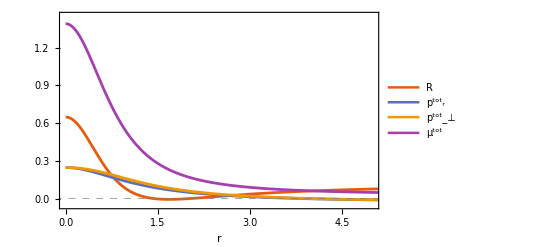

```mathematica
Plot[{R[r,-1.25,0.3,1.5,7.3],prT[r,-1.25,0.3,1.5,7.3],pperpT[r,-1.25,0.3,1.5,7.3],μT[r,-1.25,0.3,1.5,7.3]}, {r, 0, 30},AxesOrigin->{
0,0},PlotRange->{{0,5},{-0.05,1.45}},GridLines->{{}, {0}},GridLinesStyle->Directive[Gray,Dashed,Thick],PlotStyle->{Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005]},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"R","(p^tot)_r","(p^tot)_⊥","μ^tot"},LegendFunction->"Frame",LabelStyle->{FontSize->32, FontFamily->"Times"}],{0.89,0.67}],LabelStyle->{FontSize->32, FontFamily->"Times"}, Frame->{{True,True},{True,True}},FrameLabel->{r,""}, ImageSize->Full]
```

```mathematica
prT[3.9105448,-1.25,0.3,1.5,7.3]
```

6.7554×10^-12

```mathematica
prT[0.0000001,-0.8,0.3,1.5,10^10]
```

0.0105059

```mathematica
pperpT[0.00000001,-0.8,0.3,1.5,10^10]
```

0.0101507

```mathematica
Limit[R[r,a,b,c,d],r->Infinity]
```

6/d^2

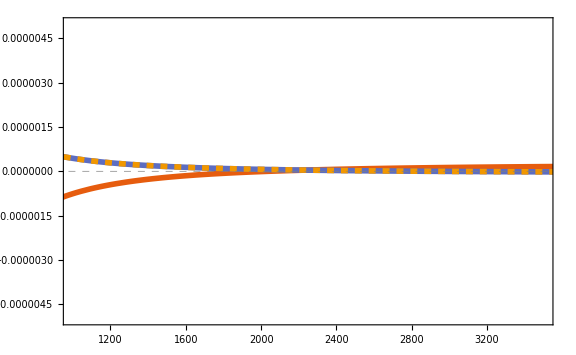

```mathematica
boundary=Plot[{R[r,-1.25,0.3,1.5,5000],prT[r,-1.25,0.3,1.5,5000],pperpT[r,-1.25,0.3,1.5,5000]}, {r, 0, 9000},AxesOrigin->{
0,0},PlotRange->{{1000,3500},{-5*10^-6,5*10^-6}},GridLines->{{}, {0}},GridLinesStyle->Directive[Gray,Dashed,Thick],PlotStyle->{Thickness[0.007],Thickness[0.007],{Thickness[0.007],Dashed}},PlotTheme->"Scientific",LabelStyle->{FontSize->32, FontFamily->"Times"}, Frame->{{True,True},{True,True}}, ImageSize->Large]
```

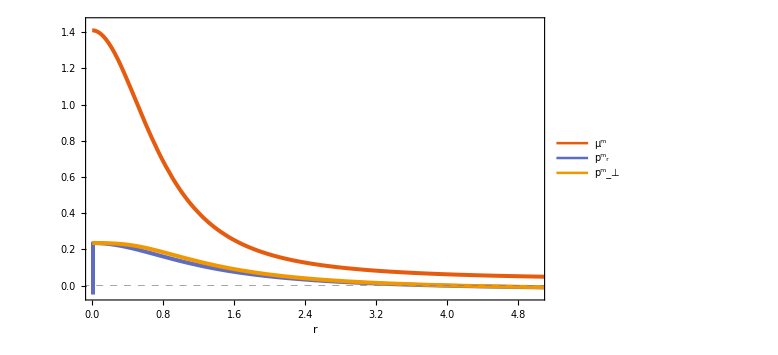

```mathematica
Plot[{μm[r,0.001,-1.25,0.3,1.5,7.3],prm[r,0.001,-1.25,0.3,1.5,7.3],pperpm[r,0.001,-1.25,0.3,1.5,7.3]}, {r, 0, 30},AxesOrigin->{
0,0},PlotRange->{{0.025,5},{-0.05,1.45}},GridLines->{{}, {0}},GridLinesStyle->Directive[Gray,Dashed,Thick],PlotStyle->{Thickness[0.005],Thickness[0.005],Thickness[0.005]},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"μ^m","(p^m)_r","(p^m)_⊥"},LegendFunction->"Frame",LabelStyle->{FontSize->32, FontFamily->"Times"}],{0.88,0.73}],LabelStyle->{FontSize->32, FontFamily->"Times"}, Frame->{{True,True},{True,True}},FrameLabel->{r,""}, ImageSize->Large]
```

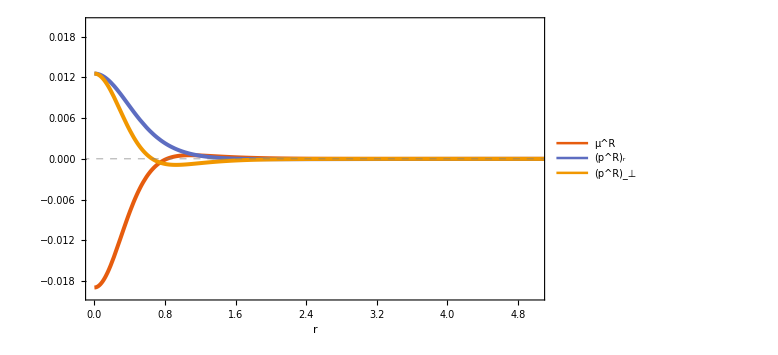

```mathematica
Plot[{μR[r,0.001,-1.25,0.3,1.5,7.3],prR[r,0.001,-1.25,0.3,1.5,7.3],pperpR[r,0.001,-1.25,0.3,1.5,7.3]}, {r, 0, 30},PlotRange->{{0,5},{-0.02,0.02}},GridLines->{{}, {0}},GridLinesStyle->Directive[Gray,Dashed,Thick],PlotStyle->{Thickness[0.005],Thickness[0.005],Thickness[0.005]},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"μ^R","(p^R)_r","(p^R)_⊥"},LegendFunction->"Frame",LabelStyle->{FontSize->28, FontFamily->"Times"}],{0.88,0.4}],LabelStyle->{FontSize->32, FontFamily->"Times"}, Frame->{{True,True},{True,True}},FrameLabel->{r,""}, ImageSize->Large]
```

```mathematica
sostotradial=D[prT[r,-1.25,0.3,1.5,7.3],r]/D[μT[r,-1.25,0.3,1.5,7.3],r];
sostotperp=D[pperpT[r,-1.25,0.3,1.5,7.3],r]/D[μT[r,-1.25,0.3,1.5,7.3],r];
sosmattradial=D[prm[r,0.001,-1.25,0.3,1.5,7.3],r]/D[μm[r,0.001,-1.25,0.3,1.5,7.3],r];
sosmattperp=D[pperpm[r,0.001,-1.25,0.3,1.5,7.3],r]/D[μm[r,0.001,-1.25,0.3,1.5,7.3],r];
```

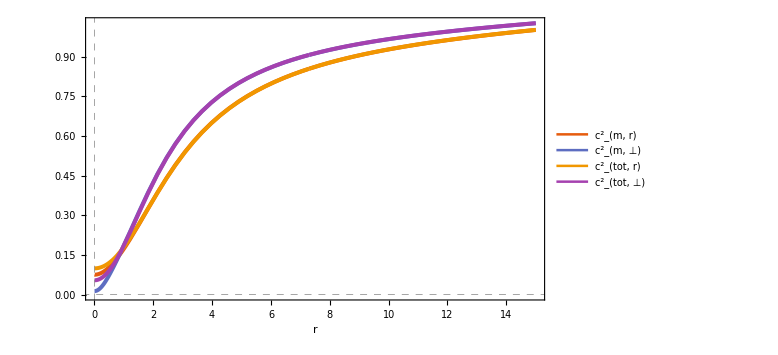

```mathematica
Plot[{sosmattradial,sosmattperp,sostotradial,sostotperp}, {r, 0.005, 15},AxesOrigin->{
0,0},GridLines->{{0}, {0}},GridLinesStyle->Directive[Gray,Dashed,Thick],PlotStyle->{Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005]},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"(c^2)_(m,  r)","(c^2)_(m,   ⊥)","(c^2)_(tot,  r)","(c^2)_(tot,   ⊥)"},LegendFunction->"Frame",LabelStyle->{FontSize->32, FontFamily->"Times"}],{0.86,0.45}],LabelStyle->{FontSize->28, FontFamily->"Times"}, Frame->{{True,True},{True,True}},FrameLabel->{r,""}, ImageSize->Large]
```

## Plots varying α:

### The following parameter constants has the same values as before: μ_1 = -1.09; c_1 = 0.3; A = 2.3; ℛ = 5000.

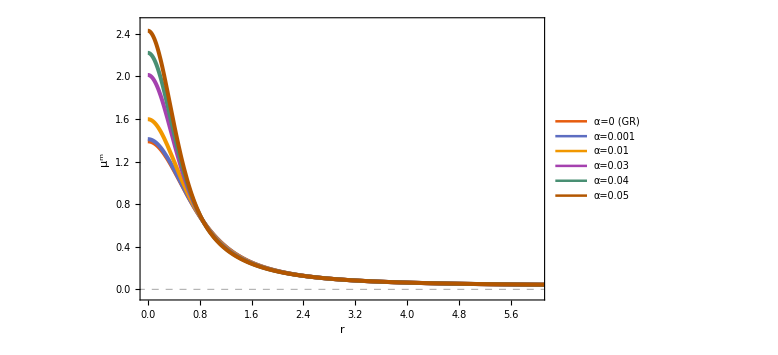

```mathematica
Plot[{μm[r,0,-1.25,0.3,1.5,7.3],μm[r,0.001,-1.25,0.3,1.5,7.3],μm[r,0.01,-1.25,0.3,1.5,7.3],μm[r,0.03,-1.25,0.3,1.5,7.3],μm[r,0.04,-1.25,0.3,1.5,7.3],μm[r,0.05,-1.25,0.3,1.5,7.3]}, {r, 0, 10},PlotRange->{{0,6},{-0.05,2.5}},AxesOrigin->{0,0},GridLines->{{}, {0}},GridLinesStyle->Directive[Gray,Dashed,Thick],PlotStyle->{Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005]},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"α=0 (GR)","α=0.001","α=0.01","α=0.03","α=0.04","α=0.05"},LegendFunction->"Frame",LabelStyle->{FontSize->24, FontFamily->"Times"}],{0.84,0.58}],LabelStyle->{FontSize->32, FontFamily->"Times"}, Frame->{{True,True},{True,True}},FrameLabel->{r,"μ^m"}, ImageSize->Large]
```

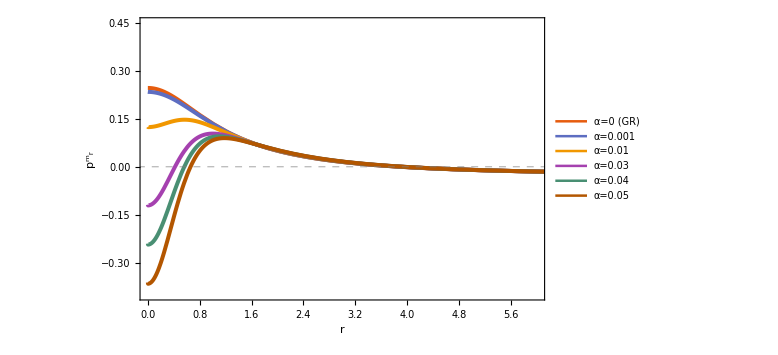

```mathematica
Plot[{prm[r,0,-1.25,0.3,1.5,7.3],prm[r,0.001,-1.25,0.3,1.5,7.3],prm[r,0.01,-1.25,0.3,1.5,7.3],prm[r,0.03,-1.25,0.3,1.5,7.3],prm[r,0.04,-1.25,0.3,1.5,7.3],prm[r,0.05,-1.25,0.3,1.5,7.3]}, {r, 0.0005, 10},PlotRange->{{0,6},{-0.4,0.45}},AxesOrigin->{0,0},GridLines->{{}, {0}},GridLinesStyle->Directive[Gray,Dashed,Thick],PlotStyle->{Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005]},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"α=0 (GR)","α=0.001","α=0.01","α=0.03","α=0.04","α=0.05"},LegendFunction->"Frame",LabelStyle->{FontSize->24, FontFamily->"Times"}],{0.84,0.58}],LabelStyle->{FontSize->32, FontFamily->"Times"}, Frame->{{True,True},{True,True}},FrameLabel->{r,"(p^m)_r"}, ImageSize->Large]
```

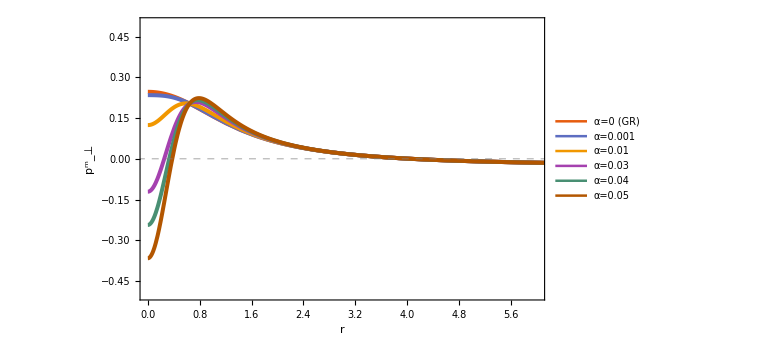

```mathematica
Plot[{pperpm[r,0,-1.25,0.3,1.5,7.3],pperpm[r,0.001,-1.25,0.3,1.5,7.3],pperpm[r,0.01,-1.25,0.3,1.5,7.3],pperpm[r,0.03,-1.25,0.3,1.5,7.3],pperpm[r,0.04,-1.25,0.3,1.5,7.3],pperpm[r,0.05,-1.25,0.3,1.5,7.3]}, {r, 0.0005, 10},PlotRange->{{0,6},{-0.5,0.5}},AxesOrigin->{0,0},GridLines->{{}, {0}},GridLinesStyle->Directive[Gray,Dashed,Thick],PlotStyle->{Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005]},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"α=0 (GR)","α=0.001","α=0.01","α=0.03","α=0.04","α=0.05"},LegendFunction->"Frame",LabelStyle->{FontSize->24, FontFamily->"Times"}],{0.84,0.51}],LabelStyle->{FontSize->32, FontFamily->"Times"}, Frame->{{True,True},{True,True}},FrameLabel->{r,"(p^m)_⊥"}, ImageSize->Large]
```

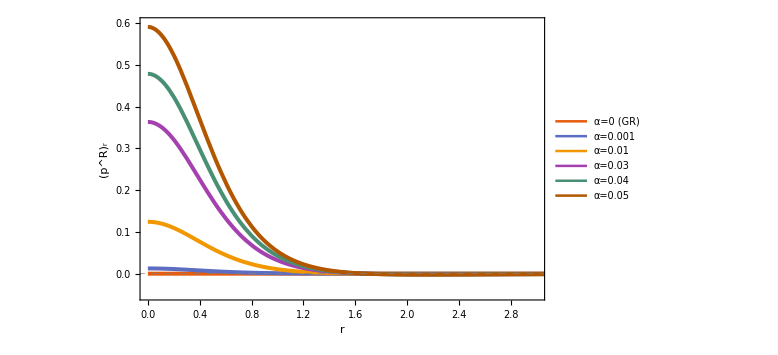

```mathematica
Plot[{prR[r,0,-1.25,0.3,1.5,7.3],prR[r,0.001,-1.25,0.3,1.5,7.3],prR[r,0.01,-1.25,0.3,1.5,7.3],prR[r,0.03,-1.25,0.3,1.5,7.3],prR[r,0.04,-1.25,0.3,1.5,7.3],prR[r,0.05,-1.25,0.3,1.5,7.3]}, {r, 0.0005, 10},PlotRange->{{0,3},{-0.05,0.6}},AxesOrigin->{0,0},GridLines->{{}, {0}},GridLinesStyle->Directive[Gray,Dashed,Thick],PlotStyle->{Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005]},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"α=0 (GR)","α=0.001","α=0.01","α=0.03","α=0.04","α=0.05"},LegendFunction->"Frame",LabelStyle->{FontSize->20, FontFamily->"Times"}],{0.85,0.6}],LabelStyle->{FontSize->32, FontFamily->"Times"}, Frame->{{True,True},{True,True}},FrameLabel->{r,"(p^R)_r"}, ImageSize->Large]
```

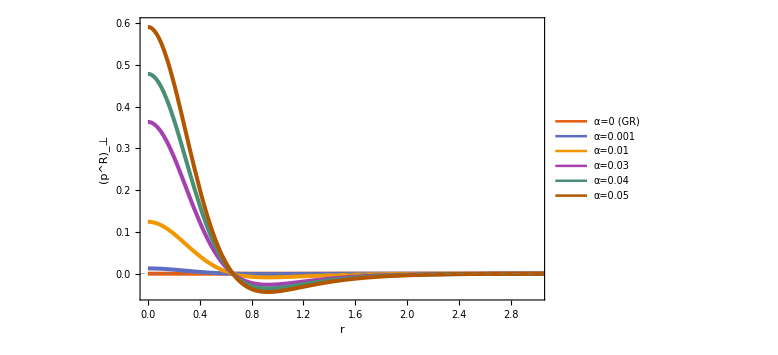

```mathematica
Plot[{pperpR[r,0,-1.25,0.3,1.5,7.3],pperpR[r,0.001,-1.25,0.3,1.5,7.3],pperpR[r,0.01,-1.25,0.3,1.5,7.3],pperpR[r,0.03,-1.25,0.3,1.5,7.3],pperpR[r,0.04,-1.25,0.3,1.5,7.3],pperpR[r,0.05,-1.25,0.3,1.5,7.3]}, {r, 0.0005, 10},PlotRange->{{0,3},{-0.05,0.6}},AxesOrigin->{0,0},GridLines->{{}, {0}},GridLinesStyle->Directive[Gray,Dashed,Thick],PlotStyle->{Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005]},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"α=0 (GR)","α=0.001","α=0.01","α=0.03","α=0.04","α=0.05"},LegendFunction->"Frame",LabelStyle->{FontSize->20, FontFamily->"Times"}],{0.85,0.6}],LabelStyle->{FontSize->32, FontFamily->"Times"}, Frame->{{True,True},{True,True}},FrameLabel->{r,"(p^R)_⊥"}, ImageSize->Large]
```

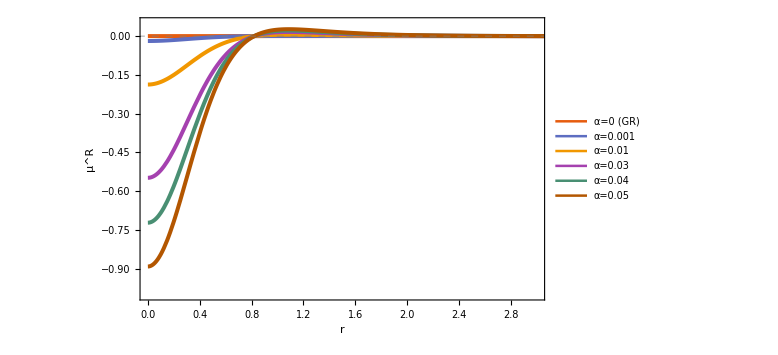

```mathematica
Plot[{μR[r,0,-1.25,0.3,1.5,7.3],μR[r,0.001,-1.25,0.3,1.5,7.3],μR[r,0.01,-1.25,0.3,1.5,7.3],μR[r,0.03,-1.25,0.3,1.5,7.3],μR[r,0.04,-1.25,0.3,1.5,7.3],μR[r,0.05,-1.25,0.3,1.5,7.3]}, {r, 0.0005, 10},PlotRange->{{0,3},{-1,0.05}},AxesOrigin->{0,0},GridLines->{{}, {0}},GridLinesStyle->Directive[Gray,Dashed,Thick],PlotStyle->{Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005]},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"α=0 (GR)","α=0.001","α=0.01","α=0.03","α=0.04","α=0.05"},LegendFunction->"Frame",LabelStyle->{FontSize->20, FontFamily->"Times"}],{0.85,0.41}],LabelStyle->{FontSize->32, FontFamily->"Times"}, Frame->{{True,True},{True,True}},FrameLabel->{r,"μ^R"}, ImageSize->Large]
```

```mathematica
sosmattradialvaryα=D[prm[r,α,-1.25,0.3,1.5,7.3],r]/D[μm[r,α,-1.25,0.3,1.5,7.3],r];
sosmattperpvaryα=D[pperpm[r,α,-1.25,0.3,1.5,7.3],r]/D[μm[r,α,-1.25,0.3,1.5,7.3],r];
sosRradialvaryα=D[prR[r,α,-1.25,0.3,1.5,7.3],r]/D[μR[r,α,-1.25,0.3,1.5,7.3],r];
sosRperpvaryα=D[pperpR[r,α,-1.25,0.3,1.5,7.3],r]/D[μR[r,α,-1.25,0.3,1.5,7.3],r];
```

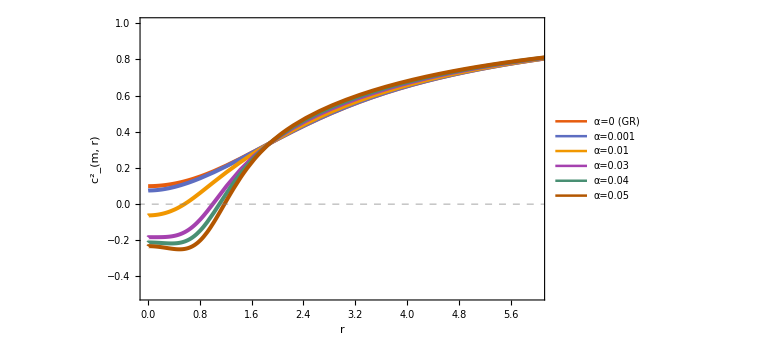

```mathematica
Plot[{sosmattradialvaryα/.α->0,sosmattradialvaryα/.α->0.001,sosmattradialvaryα/.α->0.01,sosmattradialvaryα/.α->0.03,sosmattradialvaryα/.α->0.04,sosmattradialvaryα/.α->0.05}, {r, 0.005, 10},PlotRange->{{0,6},{-0.5,1}},AxesOrigin->{0,0},GridLines->{{}, {0}},GridLinesStyle->Directive[Gray,Dashed,Thick],PlotStyle->{Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005]},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"α=0 (GR)","α=0.001","α=0.01","α=0.03","α=0.04","α=0.05"},LegendFunction->"Frame",LabelStyle->{FontSize->20, FontFamily->"Times"}],{0.86,0.42}],LabelStyle->{FontSize->32, FontFamily->"Times"}, Frame->{{True,True},{True,True}},FrameLabel->{r,"(c^2)_(m,  r)"}, ImageSize->Large]
```

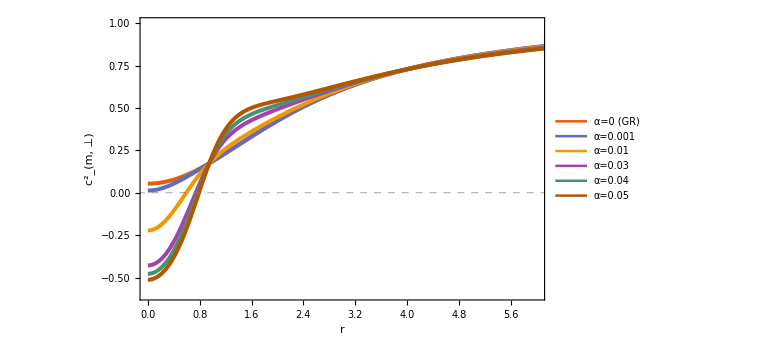

```mathematica
Plot[{sosmattperpvaryα/.α->0,sosmattperpvaryα/.α->0.001,sosmattperpvaryα/.α->0.01,sosmattperpvaryα/.α->0.03,sosmattperpvaryα/.α->0.04,sosmattperpvaryα/.α->0.05}, {r, 0.0005, 10},PlotRange->{{0,6},{-0.6,1}},AxesOrigin->{0,0},GridLines->{{}, {0}},GridLinesStyle->Directive[Gray,Dashed,Thick],PlotStyle->{Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005],Thickness[0.005]},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{"α=0 (GR)","α=0.001","α=0.01","α=0.03","α=0.04","α=0.05"},LegendFunction->"Frame",LabelStyle->{FontSize->19, FontFamily->"Times"}],{0.86,0.36}],LabelStyle->{FontSize->32, FontFamily->"Times"}, Frame->{{True,True},{True,True}},FrameLabel->{r,"(c^2)_(m,   ⊥)"}, ImageSize->Large]
```